```mathematica
ClearAll["Global`*"]
```

```mathematica
coord={t,r,θ,ϕ};
gdown={{Am[r],0,0,0},{0,-Bm[r],0,0},{0,0,-Cm[r],0},{0,0,0,-Cm[r]}}/.{θ->π/2};
gup=Simplify[Inverse[gdown]];
gupMatrix=Table[gup⟦i,j⟧,{i,1,4},{j,1,4}];
pdown={pt,pr,0,pphi};
pup=Table[∑_(j=1)^4 gupMatrix⟦i,j⟧ pdown⟦j⟧,{i,1,4}];
Vt=1/(√Am[r]);
n[r_,ω_]:=√(1-ωe[r]^2/ω^2);
n∞:=√(1-ϵ^2);
RedShift={ω->(ω∞)/(√Am[r])};
H=Simplify[1/2 (∑_(i=1)^4 ∑_(j=1)^4 gupMatrix⟦i,j⟧ pdown⟦i⟧ pdown⟦j⟧+(n[r,ω]^2-1) (pdown⟦1⟧ Vt)^2)];
dxtdλ=D[H, pt];
dxrdλ=D[H, pr];
dxϕdλ=D[H, pphi];
ptConst=-ħ ω∞;
pphiConst=n∞*ħ ω∞ b;
HSimplified=Simplify[H/.{pt->ptConst,pphi->pphiConst,ωe[r]^2->(ω∞)^2 ϵ[r]^2}/.RedShift];
Print["Hamiltonian H = ",HSimplified];
prSol=Solve[HSimplified==0,pr,Reals]⟦2⟧;
dϕdλ=dxϕdλ/.{pt->ptConst,pphi->pphiConst};
drdλ=dxrdλ/.{pt->ptConst,pphi->pphiConst}/.prSol;
Assumption1={ω∞∈Reals,ω∞>0,0<Am[r]<1,Bm[r]>1,r0>0};
Simplify[dϕdλ/drdλ,Assumptions->{ħ∈Reals,r>0,ω>0,ħ>0}];
Refine[%,Am[r]∈Reals&&ω∞>0&&Am[r]>0&&Cm[r]>0&&Bm[r]>0];
dϕdr=Refine[%,Bm[r]>0&&{-ϵ^2+1/Am[r]-b^2/Cm[r]}∈Reals];
Print["dϕ/dr = ",dϕdr(*/.ϵ[r]->(k √(r^-h))/(ω∞)*)];
```

Hamiltonian H = 1/2 (ħ^2 (ω∞)^2 (-ϵ^2+1/Am[r])-pr^2/Bm[r]+(ħ^2 b^2 (-1+ϵ^2) (ω∞)^2)/Cm[r])

dϕ/dr = ConditionalExpression[(b √(1-ϵ^2) √Am[r] Bm[r] √(1/(Bm[r] Cm[r])))/(√(Cm[r]+Am[r] (b^2 (-1+ϵ^2)-ϵ^2 Cm[r]))), ]

```mathematica
replacement:=(1-(2 M)/r) (-b^2/r^2-ϵ^2)->-u^2;
du=D[√((1-(2 M)/r) (b^2/r^2+ϵ^2))//.{r->1/x},x]dx(*/.dx ->D[1/r,r]dr*)
```

(dx (2 b^2 x (1-2 M x)-2 M (b^2 x^2+ϵ^2)))/(2 √((1-2 M x) (b^2 x^2+ϵ^2)))

```mathematica
b/(r^2 √(1+(1-(2 M)/r) (-b^2/r^2-ϵ^2)))dr/.replacement
%/.dr->-r^2 dx(*dx=D[1/r,r]dr*)
%/.dx->dx/du (*dU*)
```

(b dr)/(r^2 √(1-u^2))

-(b dx)/(√(1-u^2))

-(2 b √((1-2 M x) (b^2 x^2+ϵ^2)))/(√(1-u^2) (2 b^2 x (1-2 M x)-2 M (b^2 x^2+ϵ^2)))

需要对被积函数作变量代换，把x=1/r用u表示，为此需要反解方程(1-(2 M)/r) (-b^2/r^2-ϵ^2)==-u^2

```mathematica
(1-(2 M)/r) (b^2/r^2+ϵ^2)/.r->r0//.testparams
```

1

```mathematica
testparams={M->1,r0->10406,ϵ->(√2239)/1020,b->5301857/510};
(1-(2 M)/r) (b^2/r^2+ϵ^2)==u2/.{r->1/x}//Expand
xtou1=Solve[%,x][[3,1,2]]
xTouInN =Solve[%%/.testparams,x]/.u2->1//Simplify//N
x^2 (1-2 M x) (ϵ^2/x^2+b^2 (1-ϵ^2))==u2//Expand
xtou2=Solve[%,x][[3,1,2]] (*the third root is meaningful*)
```

b^2 x^2-2 b^2 M x^3+ϵ^2-2 M x ϵ^2==u2

1/(6 M)-((1-ⅈ √3) (-b^4+12 b^2 M^2 ϵ^2))/(6 2^(2/3) b^2 M (-2 b^6+108 b^4 M^2 u2-72 b^4 M^2 ϵ^2+√(4 (-b^4+12 b^2 M^2 ϵ^2)^3+(-2 b^6+108 b^4 M^2 u2-72 b^4 M^2 ϵ^2)^2))^(1/3))+((1+ⅈ √3) (-2 b^6+108 b^4 M^2 u2-72 b^4 M^2 ϵ^2+√(4 (-b^4+12 b^2 M^2 ϵ^2)^3+(-2 b^6+108 b^4 M^2 u2-72 b^4 M^2 ϵ^2)^2))^(1/3))/(12 2^(1/3) b^2 M)

{{x→-0.0000960799+1.17106×10^-16 ⅈ},{x→0.5+0. ⅈ},{x→0.0000960984-1.17106×10^-16 ⅈ}}

b^2 x^2-2 b^2 M x^3+ϵ^2-2 M x ϵ^2-b^2 x^2 ϵ^2+2 b^2 M x^3 ϵ^2==u2

-(b^2-b^2 ϵ^2)/(6 (-b^2 M+b^2 M ϵ^2))+((1-ⅈ √3) (-(b^2-b^2 ϵ^2)^2-12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)))/(6 2^(2/3) (-b^2 M+b^2 M ϵ^2) (-2 b^6+108 b^4 M^2 u2+6 b^6 ϵ^2-72 b^4 M^2 ϵ^2-216 b^4 M^2 u2 ϵ^2-6 b^6 ϵ^4+144 b^4 M^2 ϵ^4+108 b^4 M^2 u2 ϵ^4+2 b^6 ϵ^6-72 b^4 M^2 ϵ^6+√((-2 b^6+108 b^4 M^2 u2+6 b^6 ϵ^2-72 b^4 M^2 ϵ^2-216 b^4 M^2 u2 ϵ^2-6 b^6 ϵ^4+144 b^4 M^2 ϵ^4+108 b^4 M^2 u2 ϵ^4+2 b^6 ϵ^6-72 b^4 M^2 ϵ^6)^2+4 (-(b^2-b^2 ϵ^2)^2-12 M ϵ^2 (-b^2 M+b^2 M ϵ^2))^3))^(1/3))-1/(12 2^(1/3) (-b^2 M+b^2 M ϵ^2))(1+ⅈ √3) (-2 b^6+108 b^4 M^2 u2+6 b^6 ϵ^2-72 b^4 M^2 ϵ^2-216 b^4 M^2 u2 ϵ^2-6 b^6 ϵ^4+144 b^4 M^2 ϵ^4+108 b^4 M^2 u2 ϵ^4+2 b^6 ϵ^6-72 b^4 M^2 ϵ^6+√((-2 b^6+108 b^4 M^2 u2+6 b^6 ϵ^2-72 b^4 M^2 ϵ^2-216 b^4 M^2 u2 ϵ^2-6 b^6 ϵ^4+144 b^4 M^2 ϵ^4+108 b^4 M^2 u2 ϵ^4+2 b^6 ϵ^6-72 b^4 M^2 ϵ^6)^2+4 (-(b^2-b^2 ϵ^2)^2-12 M ϵ^2 (-b^2 M+b^2 M ϵ^2))^3))^(1/3)

```mathematica
Solve[(1-(2 M)/r) (b^2/r^2+ϵ^2)==u^2/.{r->1/x}/.testparams,x,Reals]
```

{{x→ConditionalExpression[Root[-2239+1040400 u^2+4478 #1-112438750593796 #1^2+224877501187592 #1^3&,1], ]},{x→ConditionalExpression[Root[-2239+1040400 u^2+4478 #1-112438750593796 #1^2+224877501187592 #1^3&,2], ]},{x→ConditionalExpression[Root[-2239+1040400 u^2+4478 #1-112438750593796 #1^2+224877501187592 #1^3&,3], ]}}

绘制u=√((1-(2 M)/r) (b^2/r^2+ϵ^2))关于r的函数图像，目的是对u(r)做单调性分析

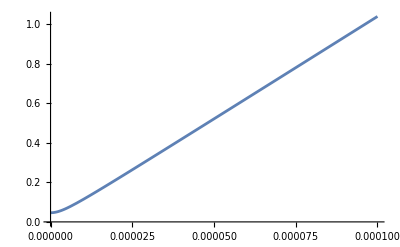

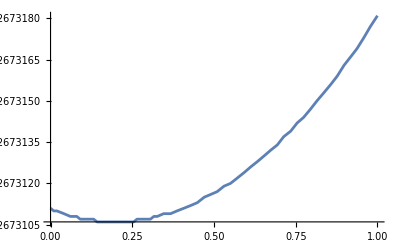

```mathematica
Plot[(√((1-2 M x) (b^2 x^2+ϵ^2)))/.testparams,{x,0,1/10^4}]
Plot[(√((1-2 M x) (b^2 x^2+ϵ^2)))/.testparams,{x,0,1/10^10}]
```

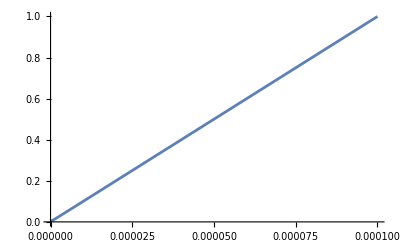

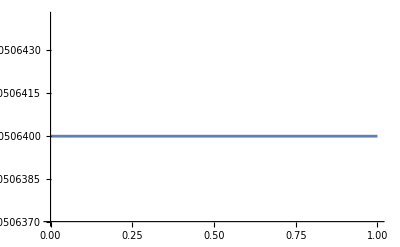

```mathematica
testparamsRN={Q->2/5,M->1,r0->10000,ϵ->(√(199999/624875001))/4,b->999990000/(√9997800017),ϵ2->199999/9998000016};
Plot[√((-1+2 M x-Q^2 x^2) (-ϵ^2+b^2 x^2 (-1+ϵ^2)))/.testparamsRN,{x,0,1/10^4}]
Plot[√((-1+2 M x-Q^2 x^2) (-ϵ^2+b^2 x^2 (-1+ϵ^2)))/.testparamsRN,{x,0,1/10^12}]
```

u’(r)的零点有两个，为寻找有意义的根，代入testparams计算，可以看到第二个根是有意义的。

```mathematica
Solve[D[√((1-(2 M)/r) (b^2/r^2+ϵ^2)), r]==0,r]/.testparams;
N[r/.%⟦1⟧]
N[r/.%%⟦2⟧]
```

3.

5.02183×10^10

求解u(r)的极小值点，记之为r1

```mathematica
Solve[D[√((1-(2 M)/r) (b^2/r^2+ϵ^2)), r]==0,r];
r1=r/.%⟦2⟧;
Print["极小值点r1=",r1];
NMinValue[√((1-(2 M)/r) (b^2/r^2+ϵ^2))/.testparams,{r,r1-1/.testparams,r1+1/.testparams}]
NMaxValue[√((1-(2 M)/r) (b^2/r^2+ϵ^2))/.testparams,{r,r1-1/.testparams,r1+1/.testparams}]
```

极小值点r1=(b^2+√(b^4-12 b^2 M^2 ϵ^2))/(2 M ϵ^2)

0.0463903

0.0463903

```mathematica
(1-(2 M)/r) (b^2/r^2+ϵ^2)/.{r->1/x}
(b^2 (2 M-r)+r^2 (r+2 M ϵ^2-r ϵ^2))/r^3/.{r->1/x}//Simplify;
Factor[1-%]//Expand(*=u^2*)
```

(1-2 M x) (b^2 x^2+ϵ^2)

b^2 x^2-2 b^2 M x^3+ϵ^2-2 M x ϵ^2

```mathematica
x^2 (1-2 M x) (ϵ^2/x^2+b^2 (1-ϵ^2))//Expand
```

b^2 x^2-2 b^2 M x^3+ϵ^2-2 M x ϵ^2-b^2 x^2 ϵ^2+2 b^2 M x^3 ϵ^2

# 史瓦西时空

```mathematica
SchwarzschildRules={Bm[arg_]:>1/Am[arg],Am[arg_]:>1-2 M/arg,Cm[arg_]:>arg^2};
testparams={M->1,r0->10406,ϵ->(√2239)/1020,b->5301857/510};
```

## 均匀等离子体

```mathematica
ϵ[r_]=ϵ;
```

```mathematica
dϕodr=Simplify[ dϕdr//.SchwarzschildRules]//Normal
```

(b √(1-ϵ^2))/(√(r^2+(1-(2 M)/r) (-r^2 ϵ^2+b^2 (-1+ϵ^2))) Abs[r])

```mathematica
Do[s[i]=Coefficient[Normal[expr],u,i],{i,0,10}];
BaseFunction=∫_0^1 Table[u^j/(√(1-u^2)),{j,0,10}]ⅆu
```

# RN时空

```mathematica
RNRules={Bm[arg_]:>1/Am[arg],Am[arg_]:>1-(2 M)/arg+Q^2/arg^2,Cm[arg_]:>arg^2};
dϕodr=Simplify[Normal[dϕdr]//.RNRules ,(Assumptions->{r>0})]
```

(b √(1-ϵ^2))/(r √(r^2-((Q^2+r (-2 M+r)) (r^2 ϵ^2-b^2 (-1+ϵ^2)))/r^2))

```mathematica
Simplify[Expand[Denominator[dϕodr]/r^2]];
Simplify[1-%^2/.r->1/x]==u2 (*u2是u^2 的整体代换*)
xtou2=Solve[%,x][[1,1,2]];(*这里是代数求解*)
```

(-1+2 M x-Q^2 x^2) (-ϵ^2+b^2 x^2 (-1+ϵ^2))==u2

待定系数法解x(u2)

```mathematica
Expand[(-1+2 M x-Q^2 x^2) (-ϵ^2+b^2 x^2 (-1+ϵ^2))==u2];
Collect[%,x]
```

ϵ^2-2 M x ϵ^2+x^3 (-2 b^2 M+2 b^2 M ϵ^2)+x^2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)+x^4 (b^2 Q^2-b^2 Q^2 ϵ^2)==u2

#### 四次方程向三次方程退化时的奇异摄动实验

```mathematica
EE+DD x+CC x^2+BB x^3+AA x^4==0;
abcde={AA->b^2 Q^2 (1-ϵ^2),BB->2 b^2 M (ϵ^2-1),CC->b^2 (1-ϵ^2+(Q/b)^2 ϵ^2),DD->-2 M ϵ^2,EE->ϵ^2-u2};
testparamsRN={Q->2/5,M->1,r0->10000,ϵ->(√(199999/624875001))/4,b->999990000/(√9997800017),ϵ2->199999/9998000016};
FerrariRoots=Solve[AA x^4+BB x^3+CC x^2-DD x-EE==0&&x>0,x,Assumptions->AA>0&&BB<0&&CC>0&&DD<0&&EE>0];(*解析求解四次方程*)
```

Values 函数是将替换规则右侧的表达式提取出来的技巧，但打印x1还会发现外面套了个大括号，所以还得取[[1]]

```mathematica
{x1,x2}=Sort@Values@FerrariRoots;
```

```mathematica
Series[Normal[x1⟦1⟧],{AA,0,1}]
Series[Normal[x2⟦1⟧],{AA,0,1}]
```

Root::sbr: 因为分支切割，级数可能表示对于 {BB,CC,DD,EE,AA} 的某些值，-EE-DD #1+CC #1^2+BB #1^3+AA #1^4& 的一个不同的根.

Root[-EE-DD #1+CC #1^2+BB #1^3&,2]+(((CC EE)/BB^2+((CC DD-BB EE) Root[-EE-DD #1+CC #1^2+BB #1^3&,2])/BB^2+((-CC^2-BB DD) Root[-EE-DD #1+CC #1^2+BB #1^3&,2]^2)/BB^2) AA)/(-DD+2 CC Root[-EE-DD #1+CC #1^2+BB #1^3&,2]+3 BB Root[-EE-DD #1+CC #1^2+BB #1^3&,2]^2)+O[AA]^2

Series::nmer: Root[-EE-DD #1+CC #1^2+BB #1^3+AA #1^4&,4] 不是一个位于 0 的关于 AA 的亚纯函数.

Series[Root[-EE-DD #1+CC #1^2+BB #1^3+AA #1^4&,4],{AA,0,1}]

两个正实根的在AA->0时的行为不同，猜想第四个根奇异摄动，第二个根退化为三次方程的实根。
接下来从数值上验证这两个猜想。

```mathematica
Normal[x1⟦1⟧]/.abcde/.testparamsRN/.u2->1
Normal[x2⟦1⟧]/.abcde/.testparamsRN/.u2->1
```

Root-0.522Root[-249955000375-9999950 #1+24999500002500799996 #1^2+49999000005000000000 #1^3+3999920000400000000 #1^4&,2]-0.5217803612708174

Root1.00 × 10^-4Root[-249955000375-9999950 #1+24999500002500799996 #1^2+49999000005000000000 #1^3+3999920000400000000 #1^4&,4]0.00009998200380859334

第一个根是负根，这意味着在方程的系数确定之前，&&x>0并不能有效地筛选出正实根。所以需要对四个根都取AA=0的极限，并且数值分析奇异摄动的行为。

```mathematica
Series[Root[-EE-DD #1+CC #1^2+BB #1^3+AA #1^4&,1],{AA,0,1}]
Series[Root[-EE-DD #1+CC #1^2+BB #1^3+AA #1^4&,2],{AA,0,1}]
Series[Root[-EE-DD #1+CC #1^2+BB #1^3+AA #1^4&,3],{AA,0,1}]
Series[Root[-EE-DD #1+CC #1^2+BB #1^3+AA #1^4&,4],{AA,0,1}]
```

Root::sbr: 因为分支切割，级数可能表示对于 {BB,CC,DD,EE,AA} 的某些值，-EE-DD #1+CC #1^2+BB #1^3+AA #1^4& 的一个不同的根.

Root[-EE-DD #1+CC #1^2+BB #1^3&,1]+(((CC EE)/BB^2+((CC DD-BB EE) Root[-EE-DD #1+CC #1^2+BB #1^3&,1])/BB^2+((-CC^2-BB DD) Root[-EE-DD #1+CC #1^2+BB #1^3&,1]^2)/BB^2) AA)/(-DD+2 CC Root[-EE-DD #1+CC #1^2+BB #1^3&,1]+3 BB Root[-EE-DD #1+CC #1^2+BB #1^3&,1]^2)+O[AA]^2

Root::sbr: 因为分支切割，级数可能表示对于 {BB,CC,DD,EE,AA} 的某些值，-EE-DD #1+CC #1^2+BB #1^3+AA #1^4& 的一个不同的根.

Root[-EE-DD #1+CC #1^2+BB #1^3&,2]+(((CC EE)/BB^2+((CC DD-BB EE) Root[-EE-DD #1+CC #1^2+BB #1^3&,2])/BB^2+((-CC^2-BB DD) Root[-EE-DD #1+CC #1^2+BB #1^3&,2]^2)/BB^2) AA)/(-DD+2 CC Root[-EE-DD #1+CC #1^2+BB #1^3&,2]+3 BB Root[-EE-DD #1+CC #1^2+BB #1^3&,2]^2)+O[AA]^2

Root::sbr: 因为分支切割，级数可能表示对于 {BB,CC,DD,EE,AA} 的某些值，-EE-DD #1+CC #1^2+BB #1^3+AA #1^4& 的一个不同的根.

Root[-EE-DD #1+CC #1^2+BB #1^3&,3]+(((CC EE)/BB^2+((CC DD-BB EE) Root[-EE-DD #1+CC #1^2+BB #1^3&,3])/BB^2+((-CC^2-BB DD) Root[-EE-DD #1+CC #1^2+BB #1^3&,3]^2)/BB^2) AA)/(-DD+2 CC Root[-EE-DD #1+CC #1^2+BB #1^3&,3]+3 BB Root[-EE-DD #1+CC #1^2+BB #1^3&,3]^2)+O[AA]^2

Series::nmer: Root[-EE-DD #1+CC #1^2+BB #1^3+AA #1^4&,4] 不是一个位于 0 的关于 AA 的亚纯函数.

Series[Root[-EE-DD #1+CC #1^2+BB #1^3+AA #1^4&,4],{AA,0,1}]

可以看到只有第四个根在AA=0处有分支型奇性，数值验证四个根的行为

```mathematica
Root[EE+DD #1+CC #1^2+BB #1^3+AA #1^4&,1]/.abcde/.testparamsRN/.u2->1
Root[EE+DD #1+CC #1^2+BB #1^3+AA #1^4&,2]/.abcde/.testparamsRN/.u2->1
Root[EE+DD #1+CC #1^2+BB #1^3+AA #1^4&,3]/.abcde/.testparamsRN/.u2->1
Root[EE+DD #1+CC #1^2+BB #1^3+AA #1^4&,4]/.abcde/.testparamsRN/.u2->1
```

Root-1.00 × 10^-4Root[249945000425+2499450014249950 #1-4999860001299996 #1^2+399992000040000 #1^3&,1]-0.00009998000359853856

1/10000

Root0.522Root[249945000425+2499450014249950 #1-4999860001299996 #1^2+399992000040000 #1^3&,2]0.5217803612707824

Root12.0Root[249945000425+2499450014249950 #1-4999860001299996 #1^2+399992000040000 #1^3&,3]11.978219618732815

```mathematica
Root[EE+DD #1+CC #1^2+BB #1^3+AA #1^4&,1]/.abcde/.testparams/.u2->1/.Q->1/10^9
Root[EE+DD #1+CC #1^2+BB #1^3+AA #1^4&,2]/.abcde/.testparams/.u2->1/.Q->1/10^9
Root[EE+DD #1+CC #1^2+BB #1^3+AA #1^4&,3]/.abcde/.testparams/.u2->1/.Q->1/10^9
Root[EE+DD #1+CC #1^2+BB #1^3+AA #1^4&,4]/.abcde/.testparams/.u2->1/.Q->1/10^9
```

Root-9.62 × 10^-5Root[-270025676100000000000000000000-1164727800000000000000000000 #1+29182381438801462289000000000582363900 #1^2-58364762877602924578000000000000000000 #1^3+29182381438801462289 #1^4&,1]-0.00009618344058276679

Root9.62 × 10^-5Root[-270025676100000000000000000000-1164727800000000000000000000 #1+29182381438801462289000000000582363900 #1^2-58364762877602924578000000000000000000 #1^3+29182381438801462289 #1^4&,2]0.00009620198657159369

Root0.500Root[-270025676100000000000000000000-1164727800000000000000000000 #1+29182381438801462289000000000582363900 #1^2-58364762877602924578000000000000000000 #1^3+29182381438801462289 #1^4&,3]0.4999999814540112

Root2.00 × 10^18Root[-270025676100000000000000000000-1164727800000000000000000000 #1+29182381438801462289000000000582363900 #1^2-58364762877602924578000000000000000000 #1^3+29182381438801462289 #1^4&,4]1.9999999999999992e18

数值测试发现第四个根才是摄动奇异根，接下来数值计算史瓦西情形对应的三次方程的Cardano解：

```mathematica
+EE+DD x+CC x^2+BB x^3==0;

Root[EE+DD #1+CC #1^2+BB #1^3&,1]/.abcde/.testparams/.u2->1/.Q->0
Root[EE+DD #1+CC #1^2+BB #1^3&,2]/.abcde/.testparams/.u2->1/.Q->0
Root[EE+DD #1+CC #1^2+BB #1^3&,3]/.abcde/.testparams/.u2->1/.Q->0
```

Root-9.62 × 10^-5Root[270025676100+1164727800 #1-29182381438801462289 #1^2+58364762877602924578 #1^3&,1]-0.00009618344058276677

Root9.62 × 10^-5Root[270025676100+1164727800 #1-29182381438801462289 #1^2+58364762877602924578 #1^3&,2]0.00009620198657159369

Root0.500Root[270025676100+1164727800 #1-29182381438801462289 #1^2+58364762877602924578 #1^3&,3]0.4999999814540112

这说明RN时空的Ferrari的第123个解可以在Q->0时退化到史瓦西时空的Cardano的第123个解。并且
1. RN时空下，x应取第2根Root[-EE-DD #1+CC #1^2+BB #1^3+AA #1^4&,2]
2. Schwartz-child时空下，x应取第2根Root[-EE-DD #1+CC #1^2+BB #1^3&,2]

#### 半解析求解 -EE-DD x+CC x^2+BB x^3+AA x^4==0

Ferrari解太复杂，不利于计算雅可比因子，遂尝试待定系数法，给出u2级数形式的x

```mathematica
ClearAll[A,B,Cval,Dval,eps2]
```

```mathematica
(*A=b^2 Q^2 (1-ε^2);
B=2 b^2 M (1-ε^2);
Cval=b^2 (1-ε^2+(Q^2/b^2) ε^2);
Dval=-2 M ε^2;       
eps2=ε^2;*)
p[x_]:=AA x^4+BB x^3+CC x^2+DD x+ϵ2;

(*求 u=0 时的正实根 x0, root4*)
$Assumptions=AA>0&&BB>0&&CC>0&&DD<0&&ϵ2>0&&b>0&&Q>0&&M>0;
x0sols=Solve[p[x]==0&&x>0,x,Reals];
```

ϵ2

```mathematica
x0=x0sols⟦2,1,2⟧//Normal;
```

Nsolve[p[x]==u2,x] 画散点图$x(u2)$，某个u2对应四个x，实部虚部都画，体现分支

```mathematica
u2List=Range[-5,5,0.02];
p[x]/.abcde/.testparamsRN;
data=Table[roots=x/. NSolve[%==u2,x];{Re[#],Im[#]}&/@roots,{u2,u2List}];
```

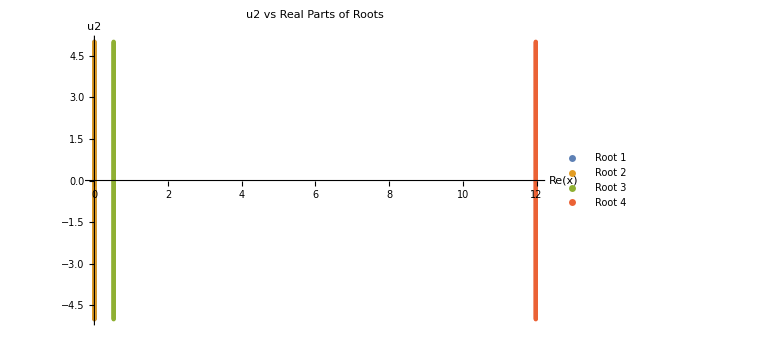

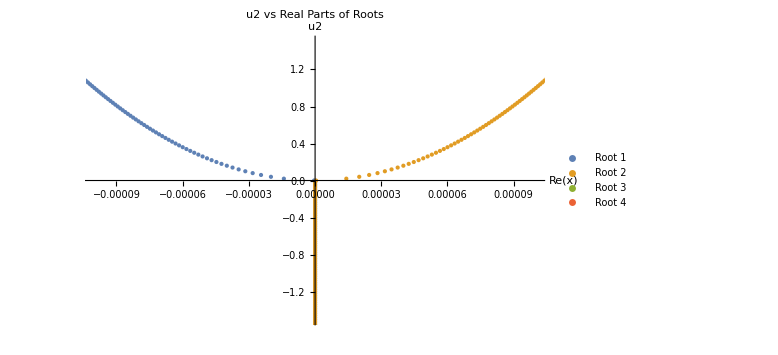

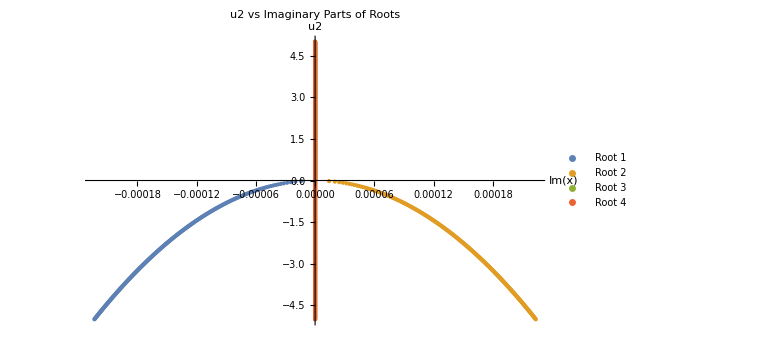

```mathematica
(*假设 reData 已经生成*)reDataSwapped=Table[Table[{data[[i,j,1]],u2List[[i]]},{i,Length[u2List]}],{j,1,4}];

imDataSwapped=Table[Table[{data[[i,j,2]],u2List[[i]]},{i,Length[u2List]}],{j,1,4}];

(*绘制实部 vs u2（横纵轴交换）*)
ListPlot[reDataSwapped,PlotStyle->PointSize[Small],PlotLegends->{"Root 1","Root 2","Root 3","Root 4"},AxesLabel->{"Re(x)","u2"},PlotLabel->"u2 vs Real Parts of Roots",ImageSize->Large]
ListPlot[reDataSwapped,PlotStyle->PointSize[Small],PlotLegends->{"Root 1","Root 2","Root 3","Root 4"},AxesLabel->{"Re(x)","u2"},PlotLabel->"u2 vs Real Parts of Roots",ImageSize->Large,PlotRange->{{-10^-4,10^-4},{-1.5,1.5}}]

(*绘制虚部 vs u2（横纵轴交换）*)
ListPlot[imDataSwapped,PlotStyle->PointSize[Small],PlotLegends->{"Root 1","Root 2","Root 3","Root 4"},AxesLabel->{"Im(x)","u2"},PlotLabel->"u2 vs Imaginary Parts of Roots",ImageSize->Large]
```

```mathematica
u2List=Range[0,0.0001,0.0000005];
p[x]/.abcde/.testparamsRN;
data=Table[roots=x/. NSolve[%==u2,x];{Re[#],Im[#]}&/@roots,{u2,u2List}];
```

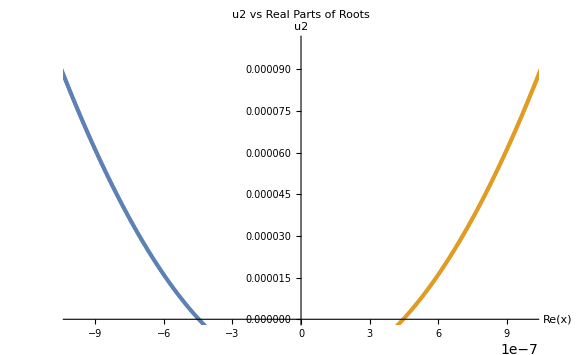

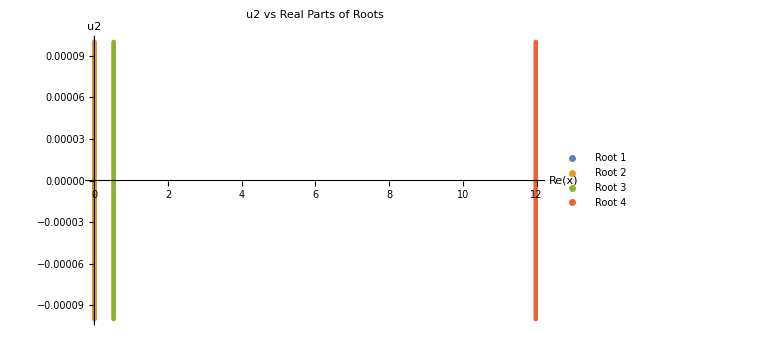

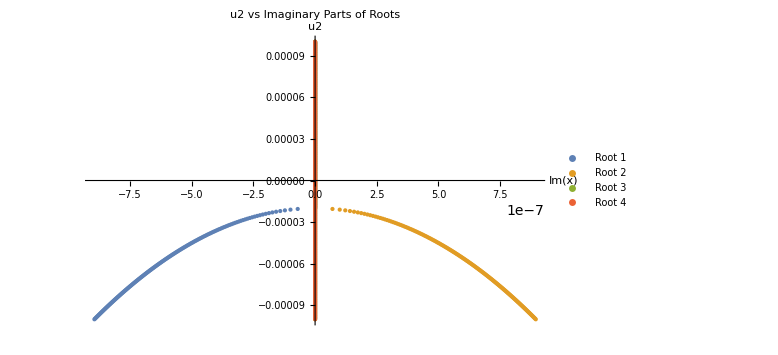

```mathematica
(*假设 reData 已经生成*)reDataSwapped=Table[Table[{data[[i,j,1]],u2List[[i]]},{i,Length[u2List]}],{j,1,4}];

imDataSwapped=Table[Table[{data[[i,j,2]],u2List[[i]]},{i,Length[u2List]}],{j,1,4}];
ListPlot[reDataSwapped,PlotStyle->PointSize[Small],(*PlotLegends->{"Root 1","Root 2","Root 3","Root 4"},*)AxesLabel->{"Re(x)","u2"},PlotLabel->"u2 vs Real Parts of Roots",ImageSize->Large,PlotRange->{{-10^-6,10^-6},{0,0.0001}}]
(*绘制实部 vs u2（横纵轴交换）*)
ListPlot[reDataSwapped,PlotStyle->PointSize[Small],PlotLegends->{"Root 1","Root 2","Root 3","Root 4"},AxesLabel->{"Re(x)","u2"},PlotLabel->"u2 vs Real Parts of Roots",ImageSize->Large]

(*绘制虚部 vs u2（横纵轴交换）*)
ListPlot[imDataSwapped,PlotStyle->PointSize[Small],PlotLegends->{"Root 1","Root 2","Root 3","Root 4"},AxesLabel->{"Im(x)","u2"},PlotLabel->"u2 vs Imaginary Parts of Roots",ImageSize->Large]
(*Plot3D[Im[Sec[(x+ⅈ y)^3]],{x,-2,2},{y,-2,2},PlotStyle->Directive[Purple,Specularity[White,20],Opacity[0.8]],Mesh->None,ClippingStyle->Automatic,PlotRange->Automatic]*)
```

#### 20260408 plotting u2[x] about x and observe the branches

```mathematica
poly=p[x]/. abcde/. testparamsRN
u2List=Range[-5,5,0.02];
data=Table[roots=x/.NSolve[poly==u2,x];({Re[#1],Im[#1]}&)/@roots,{u2,u2List}];
pts=Flatten[data,1];
```

199999/9998000016-(199999 x)/4999000008+(6249875000625199999 x^2)/62487500100-(41665833337500000 x^3)/208291667+(3333266667000000 x^4)/208291667

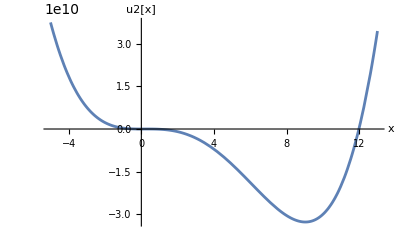

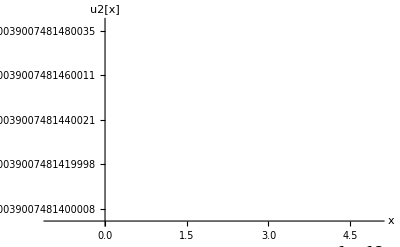

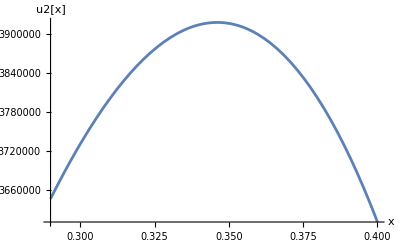

```mathematica
Plot[poly,{x,-5,13},AxesLabel->{"x","u2[x]"}]
Plot[poly,{x,-1/10^13,5/10^13},AxesLabel->{"x","u2[x]"}]
Plot[poly,{x,0.29,0.4},AxesLabel->{"x","u2[x]"}]
```

```mathematica
NSolve[poly==1,x,WorkingPrecision->16]
NSolve[poly==2,x,WorkingPrecision->16]
```

{{x→-0.00009998200340870729},{x→0.0001000020006101809},{x→0.5217803612699809},{x→11.97821961873282}}

{{x→-0.0001413893448133635},{x→0.0001414293384193055},{x→0.5217803412355603},{x→11.97821961877083}}

前两个小根对u2敏感，后两个大根对u2不敏感，且x=11.978尤甚，u2增加1，其仅变化了10^-10。这导致了复平面内画根的分布时，出现了散点凝聚在实轴0.52，11.98附近的现象。

```mathematica
NSolve[poly==-1,x,WorkingPrecision->16]
NSolve[poly==-2,x,WorkingPrecision->16]
```

{{x→-9.99779922132×10^-9-0.00009998999696072122 ⅈ},{x→-9.99779922132×10^-9+0.00009998999696072122 ⅈ},{x→0.521780401338813},{x→11.97821961865679}}

{{x→-1.99959969452×10^-8-0.0001414079135683676 ⅈ},{x→-1.99959969452×10^-8+0.0001414079135683676 ⅈ},{x→0.5217804213732246},{x→11.97821961861877}}

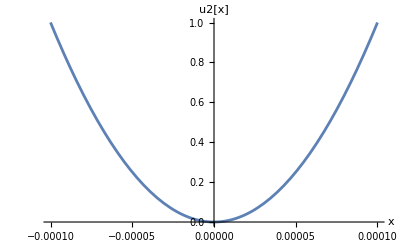

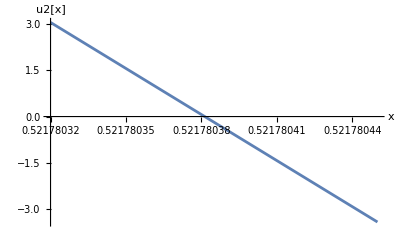

```mathematica
Plot[poly,{x,-0.0001,0.0001},AxesLabel->{"x","u2[x]"}]
Plot[poly,{x,0.52178032,0.52178045},AxesLabel->{"x","u2[x]"}]
```

画出自变量x在复平面内的区间中，poly的函数图像

```mathematica
ComplexPlot[poly,{x,-1-ⅈ,13+ⅈ},ColorFunction->"BlueGreenYellow",PlotPoints->200]
Plot3D[Abs[poly/. x->(xr+I xi)],{xr,0,13},{xi,-1,1},AxesLabel->{"Re[x]","Im[x]","|poly|"},ColorFunction->"BlueGreenYellow",PlotPoints->100]
ContourPlot[Re[poly/.x->xr+ⅈ xi],{xr,-1,13},{xi,-1,1},Contours->20,FrameLabel->{"Re[x]","Im[x]"}]
```

-Graphics-

-Graphics3D-

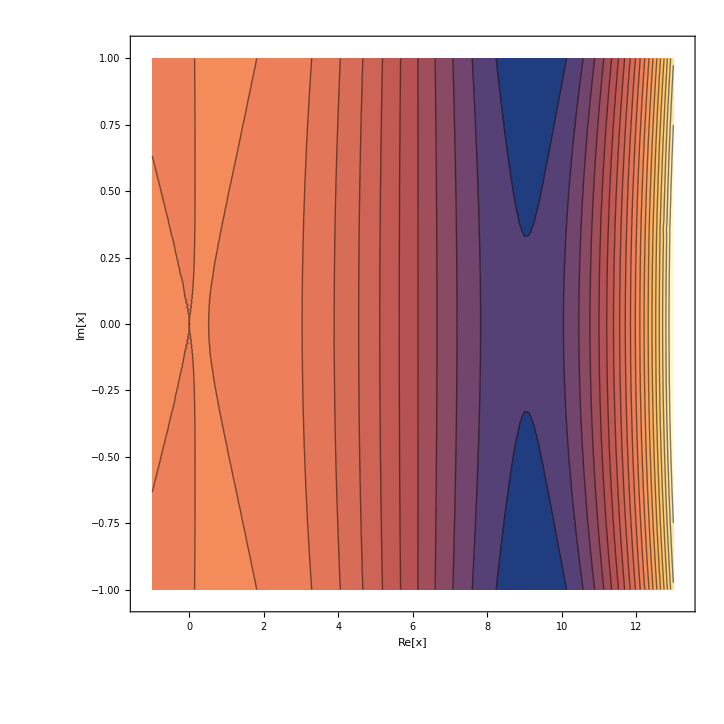

-Graphics-

-Graphics3D-

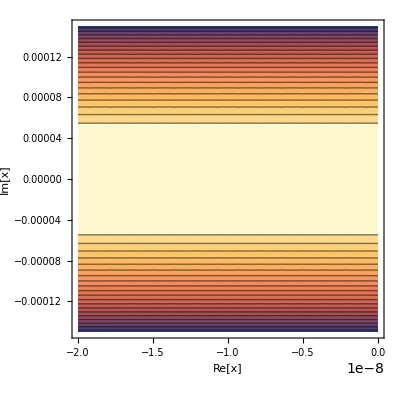

```mathematica
ComplexPlot[poly,{x,-2/10^8-0.00015ⅈ,0+0.00015ⅈ},ColorFunction->"BlueGreenYellow",PlotPoints->300,AspectRatio->1]
Plot3D[Abs[poly/. x->(xr+I xi)],{xr,-2/10^8,0},{xi,-0.00015,0.00015},AxesLabel->{"Re[x]","Im[x]","|poly|"},ColorFunction->"BlueGreenYellow",PlotPoints->100]
ContourPlot[Re[poly/.x->xr+ⅈ xi],{xr,-2/10^8,0},{xi,-0.00015,0.00015},Contours->20,FrameLabel->{"Re[x]","Im[x]"}]
```

如果要观察复根x的行为，则$u^{2}$取值应该在此区间外。

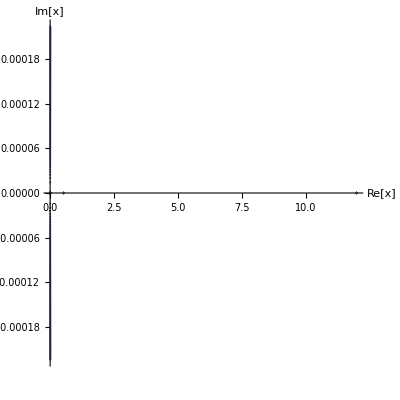

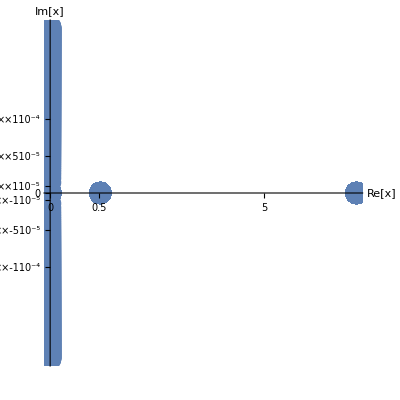

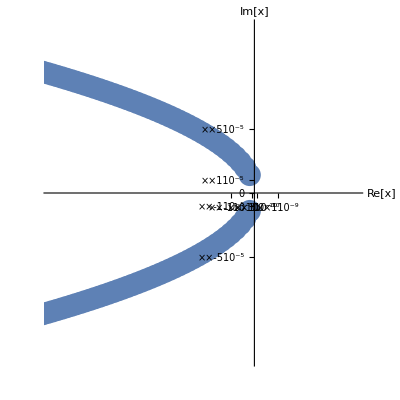

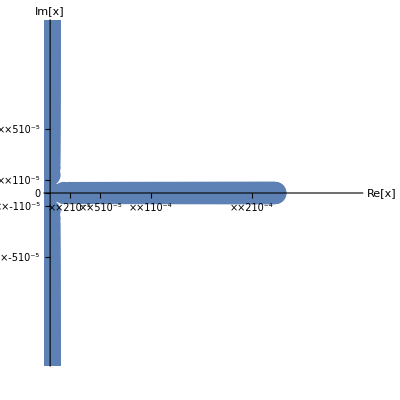

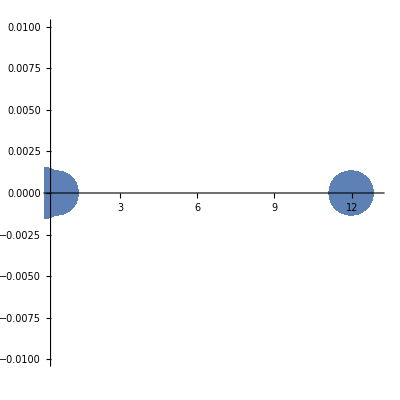

```mathematica
ListPlot[pts,PlotStyle->PointSize[0.004],AxesLabel->{"Re[x]","Im[x]"},AspectRatio->1]
ListPlot[pts,ScalingFunctions->{"SignedLog","SignedLog"},PlotStyle->PointSize[0.04],AxesLabel->{"Re[x]","Im[x]"},AspectRatio->1]
ListPlot[pts,ScalingFunctions->{"SignedLog","SignedLog"},PlotRange->{{-2/10^8,1/10^8},{-0.0003,0.0003}},AspectRatio->1,PlotStyle->PointSize[0.04],AxesLabel->{"Re[x]","Im[x]"}]
ListPlot[pts,ScalingFunctions->{"SignedLog","SignedLog"},PlotRange->{{0.0000014,0.0007},{-0.0003,0.0003}},AspectRatio->1,PlotStyle->PointSize[0.04],AxesLabel->{"Re[x]","Im[x]"}]
ListPlot[pts,PlotRange->{{0.3,13},{-0.01,0.01}},AspectRatio->1,PlotStyle->PointSize[0.08]]
```

```mathematica
(* 计算方程等式左边p(x)各阶导数*)
p1=D[p[x], x] (*p'*)
p2=D[p[x], {x,2}](*p''*)
p3=D[p[x], {x,3}](*p'''*)
p4=∂_{x,4} p[x](*p''''=24 A*)
```

DD+2 CC x+3 BB x^2+4 AA x^3

2 CC+6 BB x+12 AA x^2

6 BB+24 AA x

24 AA

```mathematica
(*逐阶计算系数*)
x1=FullSimplify[1/p1]
x2=FullSimplify[-(p2 x1^2)/(2 p1)]
x3=FullSimplify[-(p2 x1 x2+(p3 x1^3)/6)/p1]
x4=FullSimplify[-(p2 (x1 x3+x2^2/2)+p3 x1^2 x2+(p4 x1^4)/24)/p1]
```

1/(DD+2 CC x+3 BB x^2+4 AA x^3)

-(CC+3 x (BB+2 AA x))/(DD+x (2 CC+x (3 BB+4 AA x)))^3

(2 CC^2-BB DD+2 CC x (5 BB+8 AA x)+x (-4 AA DD+15 BB^2 x+56 AA x^2 (BB+AA x)))/(DD+x (2 CC+x (3 BB+4 AA x)))^5

-1/(DD+x (2 CC+x (3 BB+4 AA x)))^7(5 CC^3-8 BB CC DD+AA DD^2+29 BB CC^2 x-4 (6 BB^2+7 AA CC) DD x+3 (21 BB^2 CC+10 AA CC^2-46 AA BB DD) x^2+(63 BB^3+136 AA BB CC-184 AA^2 DD) x^3+AA (291 BB^2+44 AA CC) x^4+492 AA^2 BB x^5+328 AA^3 x^6)

```mathematica
(*输出半解析表达式,截断到前 4 阶，即u2^4*)
xApprox=x00+x1 u2+x2 u2^2+x3 u2^3+x4 u2^4/.x->x00
```

x00+u2/(DD+2 CC x00+3 BB x00^2+4 AA x00^3)-(u2^4 (5 CC^3-8 BB CC DD+AA DD^2+29 BB CC^2 x00-4 (6 BB^2+7 AA CC) DD x00+3 (21 BB^2 CC+10 AA CC^2-46 AA BB DD) x00^2+(63 BB^3+136 AA BB CC-184 AA^2 DD) x00^3+AA (291 BB^2+44 AA CC) x00^4+492 AA^2 BB x00^5+328 AA^3 x00^6))/(DD+x00 (2 CC+x00 (3 BB+4 AA x00)))^7+(u2^3 (2 CC^2-BB DD+2 CC x00 (5 BB+8 AA x00)+x00 (-4 AA DD+15 BB^2 x00+56 AA x00^2 (BB+AA x00))))/(DD+x00 (2 CC+x00 (3 BB+4 AA x00)))^5-(u2^2 (CC+3 x00 (BB+2 AA x00)))/(DD+x00 (2 CC+x00 (3 BB+4 AA x00)))^3

用testparamsRN和abcde，在u->1时做数值验证，确认解是否收敛

```mathematica
abcde={AA->b^2 Q^2 (1-ϵ^2),BB->2 b^2 M (1-ϵ^2),CC->b^2 (1-ϵ^2+(Q/b)^2 ϵ^2),DD->2 M ϵ^2,EE->ϵ^2-u2};
testparamsRN={Q->2/5,M->1,r0->10000,ϵ->(√(199999/624875001))/4,b->999990000/(√9997800017),ϵ2->199999/9998000016};
```

```mathematica
x0/.abcde/.testparamsRN/.u2->1
x1 u2/.x->x0/.abcde/.testparamsRN/.u2->1//N
x2 u2^2/.x->x0/.abcde/.testparamsRN/.u2->1//N
x3 u2^3/.x->x0/.abcde/.testparamsRN/.u2->1//N
Root[-EE-DD #1+CC #1^2+BB #1^3+AA #1^4&,4]/.abcde/.testparamsRN/.u2->1
```

Root4.47 × 10^-7Root[-4999975+9999950 #1+24999500002500799996 #1^2+49999000005000000000 #1^3+3999920000400000000 #1^4&,4]4.472165496285903e-7
0.0111782
-139.701
3.49184×10^6

Root1.00 × 10^-4Root[-249955000375-9999950 #1+24999500002500799996 #1^2+49999000005000000000 #1^3+3999920000400000000 #1^4&,4]0.00009998200380859334

```mathematica
x0/.abcde/.testparamsRN/.u2->0
xApprox/.x00->x0/.abcde/.testparamsRN/.u2->0
Root[-EE-DD #1+CC #1^2+BB #1^3+AA #1^4&,4]/.abcde/.testparamsRN/.u2->0
```

Root4.47 × 10^-7Root[-4999975+9999950 #1+24999500002500799996 #1^2+49999000005000000000 #1^3+3999920000400000000 #1^4&,4]4.472165496285903e-7

1/(199999/4999000008+(6249875000625199999 x00)/31243750050+(124997500012500000 x00^2)/208291667+(13333066668000000 x00^3)/208291667)

Root1.00 × 10^-4Root[-249955000375-9999950 #1+24999500002500799996 #1^2+49999000005000000000 #1^3+3999920000400000000 #1^4&,4]0.00009998200380859334

Root4.47 × 10^-7Root[-4999975+9999950 #1+24999500002500799996 #1^2+49999000005000000000 #1^3+3999920000400000000 #1^4&,4]4.472165496285903e-7

Root4.47 × 10^-7Root[-4999975+9999950 #1+24999500002500799996 #1^2+49999000005000000000 #1^3+3999920000400000000 #1^4&,4]4.472165496285903e-7

Root4.47 × 10^-7Root[-4999975-9999950 #1+24999500002500799996 #1^2+49999000005000000000 #1^3+3999920000400000000 #1^4&,4]4.472169496340538e-7

x1,2,3系数以近似 10⁴~10⁵ 倍的速度增长，说明该级数的收敛半径 R ≪ 1, 尝试用帕德逼近求解x关于u2的级数

```mathematica
(* ====================通用高次方程级数展开模板====================*)
testAK={a[0]->ϵ^2,a[1]->DD,a[2]->CC,a[3]->BB,a[4]->AA};
$Assumptions=a[0]>0&&a[1]<0&&a[2]>0&&a[3]>0&&a[4]>0;
n=4;
p[x_]:=∑_(k=0)^n a[k] x^k;(*a[0] 是-ε.b2 那部分，不含 u.b2*)
```

```mathematica
(*步骤1：求 u=0 时的正实根 x0，用 Root 对象表示*)
x0sols=Solve[p[x]==0&&x>0,x,Reals];
```

```mathematica
ClearAll[x0]
maxOrder=6;
(*步骤2：计算各阶导数在 x0 处的值*)
derivs=Table[D[p[x], {x,m}]/.x->x0,{m,1,maxOrder+1}]
```

{a[1]+2 x0 a[2]+3 x0^2 a[3]+4 x0^3 a[4],2 a[2]+6 x0 a[3]+12 x0^2 a[4],6 a[3]+24 x0 a[4],24 a[4],0,0,0}

```mathematica
ClearAll[xk]
```

```mathematica
(*derivs[[k]]=D[p[x],{x,k}]/. x->x0    注意 k 从 1 开始*)
xk[1]=1/derivs⟦1⟧;(*derivs[[1]]=p',derivs[[2]]=p'',...*)
(*xk[m_Integer?Positive]:=xk[m]=-1/derivs⟦1⟧(∑_(ell=1)^(m-1) 1/((ell+1)!)derivs⟦ell+1⟧∑_comp^IntegerPartitions[m-ell+1,ell] ∏_s^comp xk[Length[Partition[m-ell+1,s⟦1⟧]]]);*)

xk[2]=-(derivs⟦2⟧ xk[1]^2)/(2 derivs⟦1⟧);
xk[3]=-(derivs⟦2⟧ xk[1] xk[2]+1/6 derivs⟦3⟧ xk[1]^3)/derivs⟦1⟧;

xk[4]=-1/derivs⟦1⟧(derivs⟦2⟧ (xk[1] xk[3]+xk[2]^2/2)+derivs⟦3⟧ (xk[1]^2 xk[2])+1/24 derivs⟦4⟧ xk[1]^4);
xk[5]=-1/derivs⟦1⟧(derivs⟦2⟧ (xk[1] xk[4]+xk[2] xk[3])+derivs⟦3⟧ (xk[1]^2 xk[3]+xk[1] xk[2]^2)+derivs⟦4⟧ (xk[1]^3 xk[2])+1/120 derivs⟦5⟧ xk[1]^5);

xk[6]=-1/derivs⟦1⟧(derivs⟦2⟧ (xk[1] xk[5]+xk[2] xk[4]+xk[3]^2/2)+derivs⟦3⟧ (xk[1]^2 xk[4]+2 xk[1] xk[2] xk[3]+xk[2]^3/3)+derivs⟦4⟧ (xk[1]^3 xk[3]+xk[1] xk[2]^2 xk[1])+derivs⟦5⟧ (xk[1]^4 xk[2])+1/720 derivs⟦6⟧ xk[1]^6);
Table[xk[k],{k,1,maxOrder}];
```

```mathematica
xApprox=x0+∑_(k=1)^maxOrder xk[k] u2^k;
(*计算几种 Padé 逼近并在 u=1 处估值*)
pade51=PadeApproximant[xApprox,{u2,0,{5,1}}];
pade44=PadeApproximant[xApprox,{u2,0,{4,4}}];
pade35=PadeApproximant[xApprox,{u2,0,{3,5}}];
```

```mathematica
testAK={a[0]->ϵ^2,a[1]->DD,a[2]->CC,a[3]->BB,a[4]->AA};
p[x]/.testAK
abcde={AA->b^2 Q^2 (1-ϵ^2),BB->2 b^2 M (ϵ^2-1),CC->b^2 (1-ϵ^2+(Q/b)^2 ϵ^2),DD->-2 M ϵ^2,EE->ϵ^2-u2};
testparamsRN={Q->2/5,M->1,r0->10000,ϵ->(√(199999/624875001))/4,b->999990000/(√9997800017),ϵ2->199999/9998000016};
```

DD x+CC x^2+BB x^3+AA x^4+ϵ2

```mathematica
(*数值验证在 u=ϵ 处，x是否发散*)
x0=x0sols[[2,1,2]]//Normal; (*选物理根root2*)
{value51,value44,value35}={pade51,pade44,pade35}/.testAK/.abcde/. u2->ϵ^2/.testparamsRN//N;
{"[5/1] Padé"->value51,"[4/4] Padé"->value44,"[3/5] Padé"->value35}
```

{[5/1] Padé→4.31256×10^-13+7.33715×10^-8 ⅈ,[4/4] Padé→3.76789×10^-13+8.67953×10^-8 ⅈ,[3/5] Padé→2.89521×10^-13+9.46069×10^-8 ⅈ}

#### 待定系数法把x写成u2在0处的展开式是不合理的，尝试在u2=ϵ2处展开再用待定系数法

```mathematica
testBK={b[0]->0,b[1]->DD,b[2]->CC,b[3]->BB,b[4]->AA};
$Assumptions=b[1]<0&&b[2]>0&&b[3]>0&&b[4]>0;
n=4;
p2[x_]:=∑_(k=0)^n b[k] x^k;(*b[0] 是0，相当于ϵ^2-ϵ^2,先考虑右分支*)
p2[x]/.b[0]->0.1/.testBK/.abcde/.testparamsRN
x0sols=NSolve[%==0,x]
p2[x]/.b[0]->0.000000001/.testBK/.abcde/.testparamsRN
x0sols=NSolve[%==0,x]
p2[x]/.b[0]->0/.testBK/.abcde/.testparamsRN
x0sols=NSolve[%==0,x]
```

0.1-(199999 x)/4999000008+(6249875000625199999 x^2)/62487500100-(41665833337500000 x^3)/208291667+(3333266667000000 x^4)/208291667

{{x→-9.9962×10^-10-0.0000316199 ⅈ},{x→-9.9962×10^-10+0.0000316199 ⅈ},{x→0.52178},{x→11.9782}}

1.×10^-9-(199999 x)/4999000008+(6249875000625199999 x^2)/62487500100-(41665833337500000 x^3)/208291667+(3333266667000000 x^4)/208291667

{{x→1.99993×10^-13-3.16199×10^-9 ⅈ},{x→1.99993×10^-13+3.16199×10^-9 ⅈ},{x→0.52178},{x→11.9782}}

-(199999 x)/4999000008+(6249875000625199999 x^2)/62487500100-(41665833337500000 x^3)/208291667+(3333266667000000 x^4)/208291667

{{x→0.},{x→4.00006×10^-13},{x→0.52178},{x→11.9782}}

上面数值验证了x0=0，那么xAppox就没有零阶项。接下来用待定系数法求解xApprox

```mathematica
maxOrder=6;
(*步骤2：计算各阶导数在 x0 处的值*)
derivs=Table[D[p2[x], {x,m}]/.x->x0,{m,1,maxOrder+1}];
ClearAll[xk]
xk[1]=1/derivs⟦1⟧;(*derivs[[1]]=p',derivs[[2]]=p'',...*)
(*xk[m_Integer?Positive]:=xk[m]=-1/derivs⟦1⟧(∑_(ell=1)^(m-1) 1/((ell+1)!)derivs⟦ell+1⟧∑_comp^IntegerPartitions[m-ell+1,ell] ∏_s^comp xk[Length[Partition[m-ell+1,s⟦1⟧]]]);*)

xk[2]=-(derivs⟦2⟧ xk[1]^2)/(2 derivs⟦1⟧);
xk[3]=-(derivs⟦2⟧ xk[1] xk[2]+1/6 derivs⟦3⟧ xk[1]^3)/derivs⟦1⟧;

xk[4]=-1/derivs⟦1⟧(derivs⟦2⟧ (xk[1] xk[3]+xk[2]^2/2)+derivs⟦3⟧ (xk[1]^2 xk[2])+1/24 derivs⟦4⟧ xk[1]^4);
xk[5]=-1/derivs⟦1⟧(derivs⟦2⟧ (xk[1] xk[4]+xk[2] xk[3])+derivs⟦3⟧ (xk[1]^2 xk[3]+xk[1] xk[2]^2)+derivs⟦4⟧ (xk[1]^3 xk[2])+1/120 derivs⟦5⟧ xk[1]^5);

xk[6]=-1/derivs⟦1⟧(derivs⟦2⟧ (xk[1] xk[5]+xk[2] xk[4]+xk[3]^2/2)+derivs⟦3⟧ (xk[1]^2 xk[4]+2 xk[1] xk[2] xk[3]+xk[2]^3/3)+derivs⟦4⟧ (xk[1]^3 xk[3]+xk[1] xk[2]^2 xk[1])+derivs⟦5⟧ (xk[1]^4 xk[2])+1/720 derivs⟦6⟧ xk[1]^6);
Table[xk[k],{k,1,maxOrder}];
xApprox=x0+∑_(k=1)^maxOrder xk[k] v^k;
xApprox/.testBK/.abcde/.testparamsRN/.x0->0//N
```

-24995.1 v+1.56187×10^21 v^2-1.95192×10^38 v^3+3.04924×10^55 v^4-5.33505×10^72 v^5+1.00011×10^90 v^6

数值验证一下，在v->0-附近的xapprox和root4的结果分别是什么——振荡导致发散

```mathematica
xApprox/.testBK/.abcde/.testparamsRN/.x0->0/.{v->-(1/10^17)}//N
Root[EE+DD #1+CC #1^2+BB #1^3+AA #1^4&,4]/.abcde/.testparamsRN/.{u2->199999/9998000016-(1/10^17)}//N
xApprox/.testBK/.abcde/.testparamsRN/.x0->0/.{v->-(5/10^18)}//N
Root[EE+DD #1+CC #1^2+BB #1^3+AA #1^4&,4]/.abcde/.testparamsRN/.{u2->199999/9998000016-(5/10^18)}//N
N[xApprox/.testBK/.abcde/.testparamsRN/.x0->0/.{v->-1/10^18},60]
N[Root[EE+DD #1+CC #1^2+BB #1^3+AA #1^4&,1]/.abcde/.testparamsRN/.{u2->199999/9998000016-1/10^18},60]
```

2.43987×10^-12

2.00003×10^-13+2.4491×10^-13 ⅈ

2.39778×10^-13

2.00003×10^-13+9.9949×10^-14 ⅈ

2.67890122549124480161085953101440804759611550846193388936349×10^-14

2.67892591127845221171772827904333731890695629492500749026755×10^-14

再尝试用帕德逼近处理振荡发散

```mathematica
x0 =0;
pade57=PadeApproximant[xApprox,{v,0,{5,7}}];
pade44=PadeApproximant[xApprox,{v,0,{4,4}}];
pade35=PadeApproximant[xApprox,{v,0,{3,5}}];
{value57,value44,value35}={pade57,pade44,pade35}/.testBK/.abcde/.v->-(1/10^10)/.testparamsRN//N;
{"[5/7] Padé"->value57,"[4/4] Padé"->value44,"[3/5] Padé"->value35}
EE+DD x+CC x^2+BB x^3+AA x^4/.abcde/.testparamsRN/.{u2->199999/9998000016-(1/10^10)}//N;
NSolve[%==0,x]
```

{[5/7] Padé→-2.6028×10^-29,[4/4] Padé→-7.78055×10^-13,[3/5] Padé→-2.77196×10^-27}

{{x→2.00002×10^-13-9.9991×10^-10 ⅈ},{x→2.00002×10^-13+9.9991×10^-10 ⅈ},{x→0.52178},{x→11.9782}}

#### 尝试在近日点u2=1处展开

先试探可行域，再设法处理振荡发散（比如左支用u2-ϵ2级数，右支用u2-1级数；再比如左支用u2-1的洛朗级数，右支用u2-1的泰勒级数；再比如左支用u2-1的帕德逼近，右支用u2-1的泰勒级数……）

```mathematica
testCK={c[0]->ϵ2-1,c[1]->DD,c[2]->CC,c[3]->BB,c[4]->AA};
abcde={AA->b^2 Q^2 (1-ϵ^2),BB->2 b^2 M (ϵ^2-1),CC->b^2 (1-ϵ^2+(Q/b)^2 ϵ^2),DD->-2 M ϵ^2,EE->ϵ^2-u2};
testparamsRN={Q->2/5,M->1,r0->10000,ϵ->(√(199999/624875001))/4,b->999990000/(√9997800017),ϵ2->199999/9998000016};
$Assumptions=c[1]<0&&c[2]>0&&c[3]>0&&c[4]>0;
n=4;
p3[x_]:=∑_(k=0)^n c[k] x^k;(*b[0] 是0，相当于ϵ^2-ϵ^2,先考虑右分支*)
(*p3[x]/.c[0]->0.1/.testBK/.abcde/.testparamsRN
x0sols=NSolve[%==0,x]
p3[x]/.c[0]->0.000000001/.testBK/.abcde/.testparamsRN
x0sols=NSolve[%==0,x]
p3[x]/.c[0]->0/.testBK/.abcde/.testparamsRN
x0sols=NSolve[%==0,x]*)
```

区别于u2=ϵ2处展开，u2=1时，方程不会退化为齐次方程，因此还需计算x0. 注意到u=1时是近日点，因此x0=1/r0. 我们可以求解x0并验证根是否有物理意义。

```mathematica
(*步骤1：求 u=1 时的正实根 x0，用 Root 对象表示*)
x0sols=Solve[p3[x]==0 ,x,Reals];
x0sols[[2,1,2]]/.testCK/.abcde/.testparamsRN
p3[x]/.testCK/.abcde/.testparamsRN;
Solve[%==0&&x>0,x,Reals]
```

1/10000

{{x→1/10000},{x→Root0.522Root[249945000425+2499450014249950 #1-4999860001299996 #1^2+399992000040000 #1^3&,2]0.5217803612707824},{x→Root12.0Root[249945000425+2499450014249950 #1-4999860001299996 #1^2+399992000040000 #1^3&,3]11.978219618732815}}

由上可知, x0sols[[2,1,2]] 是有物理意义的x0, 接下来用待定系数法求解xApprox

```mathematica
maxOrder=6;
Clear[x0];
(*步骤2：计算各阶导数在 x0 处的值*)
derivs=Table[D[p3[x], {x,m}]/.x->x0,{m,1,maxOrder+1}];
ClearAll[xk]
xk[1]=1/derivs⟦1⟧;(*derivs[[1]]=p',derivs[[2]]=p'',...*)
(*xk[m_Integer?Positive]:=xk[m]=-1/derivs⟦1⟧(∑_(ell=1)^(m-1) 1/((ell+1)!)derivs⟦ell+1⟧∑_comp^IntegerPartitions[m-ell+1,ell] ∏_s^comp xk[Length[Partition[m-ell+1,s⟦1⟧]]]);*)

xk[2]=-(derivs⟦2⟧ xk[1]^2)/(2 derivs⟦1⟧);
xk[3]=-(derivs⟦2⟧ xk[1] xk[2]+1/6 derivs⟦3⟧ xk[1]^3)/derivs⟦1⟧;

xk[4]=-1/derivs⟦1⟧(derivs⟦2⟧ (xk[1] xk[3]+xk[2]^2/2)+derivs⟦3⟧ (xk[1]^2 xk[2])+1/24 derivs⟦4⟧ xk[1]^4);
xk[5]=-1/derivs⟦1⟧(derivs⟦2⟧ (xk[1] xk[4]+xk[2] xk[3])+derivs⟦3⟧ (xk[1]^2 xk[3]+xk[1] xk[2]^2)+derivs⟦4⟧ (xk[1]^3 xk[2])+1/120 derivs⟦5⟧ xk[1]^5);

xk[6]=-1/derivs⟦1⟧(derivs⟦2⟧ (xk[1] xk[5]+xk[2] xk[4]+xk[3]^2/2)+derivs⟦3⟧ (xk[1]^2 xk[4]+2 xk[1] xk[2] xk[3]+xk[2]^3/3)+derivs⟦4⟧ (xk[1]^3 xk[3]+xk[1] xk[2]^2 xk[1])+derivs⟦5⟧ (xk[1]^4 xk[2])+1/720 derivs⟦6⟧ xk[1]^6);
Table[xk[k],{k,1,maxOrder}];
xApprox=x0+∑_(k=1)^maxOrder xk[k] w2^k;
xApprox/.x0->x0sols[[2,1,2]]/.testCK/.abcde/.testparamsRN//N
```

-2.05207×10^-6 w2^6+2.73555×10^-6 w2^5-3.90711×10^-6 w2^4+6.24975×10^-6 w2^3-0.0000124992 w2^2+0.000050006 w2+0.0001

数值验证这一展开在区间（u2small-1,0]上是否收敛

```mathematica
(*计算RN时空下，u2small的数值*)
testAK={a[0]->ϵ^2,a[1]->DD,a[2]->CC,a[3]->BB,a[4]->AA};
$Assumptions=a[0]>0&&a[1]<0&&a[2]>0&&a[3]>0&&a[4]>0;
n=4;
p[x_]:=∑_(k=0)^n a[k] x^k;
u2small=N[Minimize[{p[x]/.testAK/.abcde/.testparamsRN,0≤x<=1/10^4},x],60][[1]]
```

0.0000200039007481393866403045408056369914079858631459396480846095

```mathematica
(*w2=u2small-1,即u2=u2small的情形：*)
N[xApprox/.x0->x0sols⟦2,1,2⟧/.testCK/.abcde/.testparamsRN/.w2->u2small-1,60];
p3[x]-w2/.testCK/.abcde/.testparamsRN/.{w2->u2small-1};
NSolve[%==0 ,x][[1,1,2]];
Print["级数形式的xApprox[u2small] = ",%%%,"   数值解x[u2small] = ",%]
```

0.0000200039007481393866403045408056369914079858631459396480846095

级数形式的xApprox[u2small] = 0.000022553   数值解x[u2small] = 2.0000300004011410341407×10^-13

出现奇性，所以在区间w2 ∈ {u2small - 1, 0}内，至少存在一个singularity(奇点)w2sing使得xApprox在区间w2 ∈ {w2sing, 0}有定义，接下来寻找该奇点w2sing

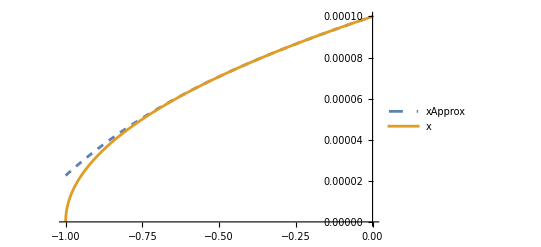

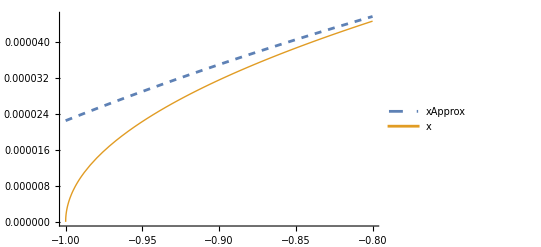

```mathematica
NxApprox[w2]=N[xApprox/.x0->x0sols⟦2,1,2⟧/.testCK/.abcde/.testparamsRN,60];
Clear[Nx];
p3[x]-w2/.testCK/.abcde/.testparamsRN;
Nx[w2_]=NSolve[%==0 ,x,Reals][[2,1,2]];
Plot[{NxApprox[w2],Nx[w2]},{w2,u2small-1,0},PlotStyle->{Dashed,Thick},PlotLegends->{"xApprox","x"}]
Plot[{NxApprox[w2],Nx[w2]},{w2,u2small-1,-0.8},PlotStyle->{Dashed,Thick},PlotLegends->{"xApprox","x"}]
```

{{x→2.00003×10^-13,w2→-0.99998},{x→0.346111,w2→3.91727×10^6},{x→9.02889,w2→-3.2732×10^10}}

{{w2→-3.27319763589529816300466134582191256151170370180850247541916033504870247703770974827780170588603476×10^10},{w2→-0.999979996099251860613359695459194363008592014136854060351915390531351764939710711435305812929690872},{w2→3.9172688373374956985244590562722435647695159333236299565320391595968859804024781366851930970817199×10^6}}

0.

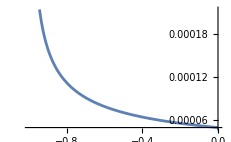

```mathematica
NSolve[{p3[x]-w2 == 0, D[p3[x], x] == 0} /. testCK /. abcde /. testparamsRN, {x, w2}]
disc=Discriminant[p3[x]-w2,x];
discNum=N[disc/.testCK/.abcde/.testparamsRN,100];
NSolve[discNum==0,w2]
%[[2,1,2]]-N[u2small-1,99]
Plot[Evaluate[D[Nx[w2], w2]], {w2,   u2small - 1, 0}]
```

这说明奇点恰是展开区域的下界w2sing=u2small-1，这意味着越靠近w2=u2small-1，|xApprox-x|就越大。因此尝试用帕德逼近来处理这一问题

```mathematica
x0=0.0001;
Npade57=PadeApproximant[NxApprox[w2],{w2,0,{5,7}}];
```

```mathematica
Npade44=PadeApproximant[NxApprox[w2],{w2,0,{4,4}}];
Npade33=PadeApproximant[NxApprox[w2],{w2,0,{3,3}}];
```

```mathematica
{value57,value44,value35}={Npade57,Npade44,Npade33}/.testCK/.abcde/.w2->-0.9/.testparamsRN//N;
{"[5/7] Padé"->value57,"[4/4] Padé"->value44,"[3/3] Padé"->value35}
```

{[5/7] Padé→0.0000350388,[4/4] Padé→0.0000338343,[3/3] Padé→0.0000322639}

```mathematica
abcde1={AA->b^2 Q^2 (1-ϵ^2),BB->2 b^2 M (ϵ^2-1),CC->b^2 (1-ϵ^2+(Q/b)^2 ϵ^2),DD->-2 M ϵ^2,EE->ϵ^2};
EE+DD x+CC x^2+BB x^3+AA x^4==w2+1/.abcde1/.testparamsRN/.{w2->-0.9}//N;
NSolve[%,x][[2,1]]
```

x→0.0000316178

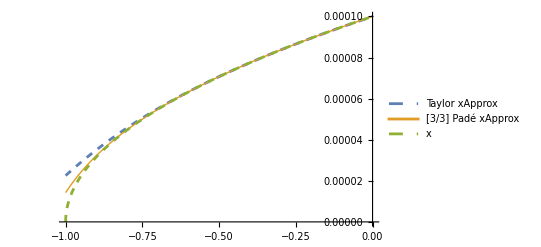

```mathematica
Plot[{NxApprox[w2],Npade33,Nx[w2]},{w2,u2small-1,0},PlotStyle->{Dashed,Thick},PlotLegends->{"Taylor xApprox","[3/3] Padé xApprox","x"}]
```

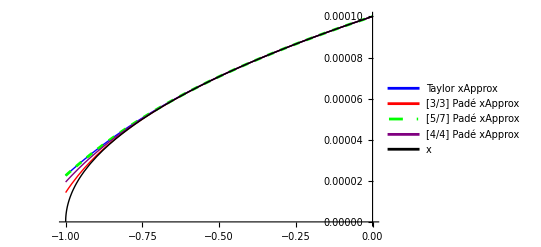

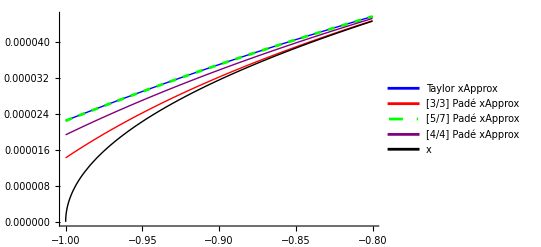

```mathematica
Plot[{NxApprox[w2],Npade33,Npade57,Npade44,Nx[w2]},{w2,u2small-1,0},PlotStyle->{{Thick,Blue},{Thick,Red},{Dashed,Green},{Thick,Purple},{Black,Thick}},PlotLegends->{"Taylor xApprox","[3/3] Padé xApprox","[5/7] Padé xApprox","[4/4] Padé xApprox","x"}]
Plot[{NxApprox[w2],Npade33,Npade57,Npade44,Nx[w2]},{w2,u2small-1,-0.8},PlotStyle->{{Thick,Blue},{Thick,Red},{Dashed,Green},{Thick,Purple},{Black,Thick}},PlotLegends->{"Taylor xApprox","[3/3] Padé xApprox","[5/7] Padé xApprox","[4/4] Padé xApprox","x"}]
```

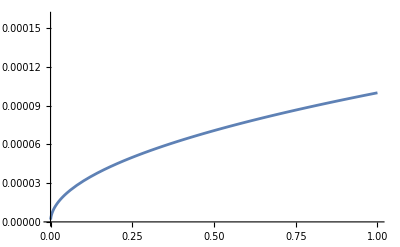

```mathematica
Plot[Nx[u-1],{u,0,1}]
```

#### 尝试提取包含奇点的根式sqrt[u2-u2small],对剩下的部分x[u2]/sqrt[u2-u2small]作展开

#### 20260406 尝试在u2=u2small处展开，待定系数法解x关于u2-u2small的Puiseux级数

```mathematica
Clear[p4]
testDK={d[0]->ϵ2-u2small,d[1]->DD,d[2]->CC,d[3]->BB,d[4]->AA};
abcde={AA->b^2 Q^2 (1-ϵ^2),BB->2 b^2 M (ϵ^2-1),CC->b^2 (1-ϵ^2+(Q/b)^2 ϵ^2),DD->-2 M ϵ^2,EE->ϵ^2-u2};
testparamsRN={Q->2/5,M->1,r0->10000,ϵ->(√(199999/624875001))/4,b->999990000/(√9997800017),ϵ2->199999/9998000016};
$Assumptions=d[1]<0&&d[2]>0&&d[3]>0&&d[4]>0;
n=4;
p4[x_]:=∑_(k=0)^n d[k] x^k;
```

```mathematica
ClearAll[xk];
maxOrder=4;
```

```mathematica
(*用 s=Sqrt[v2] 把所有幂次变成整数*)
derivs=Table[D[p4[x], {x,m}]/.x->x0,{m,1,maxOrder+2}];
xk[1]=√(2/derivs⟦2⟧);
xk[2]=-(derivs⟦3⟧ xk[1]^2)/(6 derivs⟦2⟧);
xk[3]=-(derivs⟦3⟧ (xk[1]^2 xk[2])+1/6 derivs⟦4⟧ xk[1]^3)/derivs⟦2⟧;
xk[4]=-(1/2 derivs⟦2⟧ xk[2]^2+derivs⟦3⟧ (xk[1]^2 xk[3]+xk[1] xk[2]^2)+derivs⟦4⟧ (xk[1]^3 xk[2])+1/24 derivs⟦5⟧ xk[1]^4)/derivs⟦2⟧;
```

#### 右支（红色支）去掉整数幂的puiseux级数 20260409

```mathematica
Clear[p4]
(*计算RN时空下，u2small的数值*)
testAK={a[0]->ϵ^2,a[1]->DD,a[2]->CC,a[3]->BB,a[4]->AA};
$Assumptions=a[0]>0&&a[1]<0&&a[2]>0&&a[3]>0&&a[4]>0;
n=4;
p[x_]:=∑_(k=0)^n a[k] x^k;
u2small=N[Minimize[{p[x]/.testAK/.abcde/.testparamsRN,0≤x<=1/10^4},x],60][[1]]
testDK={d[0]->ϵ2-u2small,d[1]->DD,d[2]->CC,d[3]->BB,d[4]->AA};
abcde={AA->b^2 Q^2 (1-ϵ^2),BB->2 b^2 M (ϵ^2-1),CC->b^2 (1-ϵ^2+(Q/b)^2 ϵ^2),DD->-2 M ϵ^2,EE->ϵ^2-u2};
testparamsRN={Q->2/5,M->1,r0->10000,ϵ->(√(199999/624875001))/4,b->999990000/(√9997800017),ϵ2->199999/9998000016};
$Assumptions=d[1]<0&&d[2]>0&&d[3]>0&&d[4]>0;
n=4;
p4[x_]:=∑_(k=0)^n d[k] x^k;
```

0.0000200039007481393866403045408056369914079858631459396480846095

```mathematica
Clear[xk];
maxOrder=4;
derivs=Table[D[p4[x], {x,m}]/.x->x0,{m,1,maxOrder+2}];
xk[1]=√(2/derivs⟦2⟧);
xk[3]=-(derivs⟦3⟧ xk[1]^3)/(6 derivs⟦2⟧);
xk[5]=-(1/2 derivs⟦3⟧ (3 xk[1]^2 xk[3]^2)+derivs⟦4⟧ (xk[1]^4 xk[3])+1/24 derivs⟦5⟧ xk[1]^5)/derivs⟦2⟧;
xk[7]=-1/derivs⟦2⟧(1/2 derivs⟦3⟧ (15 xk[1]^2 xk[5] xk[3]+5 xk[1] xk[3]^3)+derivs⟦4⟧ (xk[1]^4 xk[5]+6 xk[1]^3 xk[3]^2)+1/2 derivs⟦5⟧ (5 xk[1]^4 xk[3])+1/120 derivs⟦6⟧ xk[1]^5);
(* ====================半整数次幂试探解====================*)
xApproxRight=x0+xk[1] √v2+xk[3] v2^(3/2)+xk[5] v2^(5/2)+xk[7] v2^(7/2);
p4[x0]/.testDK/.abcde/.testparamsRN;
x0Numerical=NSolve[%==0&&x0>0,x0,Reals,WorkingPrecision->60][[1,1]]
xApproxRight/.testDK/.abcde
```

x0→2.0000300004011410341407120138×10^-13

x0+√2 √v2 √(1/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2)))-1/3 √2 v2^(3/2) (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2)) (1/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2)))^(5/2)-(v2^(5/2) (-32 √2 b^2 Q^2 (1-ϵ^2) (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2)) (1/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2)))^(9/2)+(2 (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2))^3)/(3 (12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2))^6)))/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2))-(v2^(7/2) (1/2 (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2)) (-(20 (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2))^3)/(27 (12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2))^8)+10 √2 (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2)) (1/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2)))^(9/2) (-32 √2 b^2 Q^2 (1-ϵ^2) (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2)) (1/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2)))^(9/2)+(2 (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2))^3)/(3 (12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2))^6)))+24 b^2 Q^2 (1-ϵ^2) (8/3 √2 (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2))^2 (1/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2)))^(13/2)-(4 (-32 √2 b^2 Q^2 (1-ϵ^2) (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2)) (1/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2)))^(9/2)+(2 (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2))^3)/(3 (12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2))^6)))/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2))^3)))/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2))

```mathematica
Clear[xApproxRightNumerical]
xApproxRightNumerical[v2_]:=xApproxRight/. x0Numerical/. testDK/. abcde/. testparamsRN//N;
xApproxRightNumerical[v2]
N[xApproxRightNumerical[v2]/.v2->1-u2small,60]
```

2.00003×10^-13+0.000099991 √v2+9.9973×10^-13 v2^(3/2)-1.91789×10^-28 v2^(5/2)-1.15092×10^-35 v2^(7/2)

0.00009999

```mathematica
(*Clear[u2small];*)
testDK={d[0]->ϵ2-u2small1,d[1]->DD,d[2]->CC,d[3]->BB,d[4]->AA};
abcde={AA->b^2 Q^2 (1-ϵ^2),BB->2 b^2 M (ϵ^2-1),CC->b^2 (1-ϵ^2+(Q/b)^2 ϵ^2),DD->-2 M ϵ^2,EE->ϵ^2-u2};
testparamsRN={Q->2/5,M->1,r0->10000,ϵ->(√(199999/624875001))/4,b->999990000/(√9997800017),ϵ2->199999/9998000016};
Clear[NxRight];
poly=p4[x]-v2/.testDK/.abcde/.testparamsRN
```

199999/9998000016-u2small1-v2-(199999 x)/4999000008+(6249875000625199999 x^2)/62487500100-(41665833337500000 x^3)/208291667+(3333266667000000 x^4)/208291667

```mathematica
NxRight[v2_]=Re[NSolve[poly==0 ,x][[2,1,2]]/.u2small1->u2small//N]
(*Plot[Nx[v2],{v2,0,1-u2small/.u2smallNumerical}]*)
```

3.125+Re[-0.5 √(34.8958+(1.67993×10^-18 (3.90609×10^37-7.49835×10^29 v2))/(3.12481×10^58-1.50714×10^52 v2+√(-4. (6.24975×10^38-1.19974×10^31 v2)^3+(3.12481×10^58-1.50744×10^42 (-3.99887×10^-8+9.998×10^9 v2))^2))^(1/3)+6.6143×10^-20 (3.12481×10^58-1.50714×10^52 v2+√(-4. (6.24975×10^38-1.19974×10^31 v2)^3+(3.12481×10^58-1.50744×10^42 (-3.99887×10^-8+9.998×10^9 v2))^2))^(1/3))+0.5 √(69.7917-(1.67993×10^-18 (3.90609×10^37-7.49835×10^29 v2))/(3.12481×10^58-1.50714×10^52 v2+√(-4. (6.24975×10^38-1.19974×10^31 v2)^3+(3.12481×10^58-1.50744×10^42 (-3.99887×10^-8+9.998×10^9 v2))^2))^(1/3)-6.6143×10^-20 (3.12481×10^58-1.50714×10^52 v2+√(-4. (6.24975×10^38-1.19974×10^31 v2)^3+(3.12481×10^58-1.50744×10^42 (-3.99887×10^-8+9.998×10^9 v2))^2))^(1/3)-410.156/(√(34.8958+(1.67993×10^-18 (3.90609×10^37-7.49835×10^29 v2))/(3.12481×10^58-1.50714×10^52 v2+√(-4. (6.24975×10^38-1.19974×10^31 v2)^3+(3.12481×10^58-1.50744×10^42 (-3.99887×10^-8+9.998×10^9 v2))^2))^(1/3)+6.6143×10^-20 (3.12481×10^58-1.50714×10^52 v2+√(-4. (6.24975×10^38-1.19974×10^31 v2)^3+(3.12481×10^58-1.50744×10^42 (-3.99887×10^-8+9.998×10^9 v2))^2))^(1/3))))]

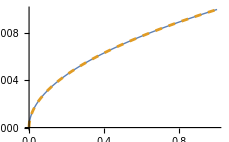
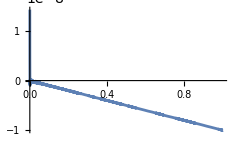

```mathematica
Plot[{xApproxRightNumerical[v2],NxRight[v2]},{v2,0,1-u2small},PlotStyle->{{Thick},{Dashed}},PlotLegends->{"Puiseux xApprox","x"}]
Plot[{xApproxRightNumerical[v2]-NxRight[v2]},{v2,0,1-u2small},PlotLegends->{"Puiseux xApprox-x"}]
```

#### 左支（绿色支）的Puiseux级数解 20260410

```mathematica
Clear[p4]
(*计算RN时空下，u2small的数值*)
testAK={a[0]->ϵ^2,a[1]->DD,a[2]->CC,a[3]->BB,a[4]->AA};
$Assumptions=a[0]>0&&a[1]<0&&a[2]>0&&a[3]>0&&a[4]>0;
n=4;
p[x_]:=∑_(k=0)^n a[k] x^k;
u2small=N[Minimize[{p[x]/.testAK/.abcde/.testparamsRN,0≤x<=1/10^4},x],60][[1]]
testDK={d[0]->ϵ2-u2small,d[1]->DD,d[2]->CC,d[3]->BB,d[4]->AA};
abcde={AA->b^2 Q^2 (1-ϵ^2),BB->2 b^2 M (ϵ^2-1),CC->b^2 (1-ϵ^2+(Q/b)^2 ϵ^2),DD->-2 M ϵ^2,EE->ϵ^2-u2};
testparamsRN={Q->2/5,M->1,r0->10000,ϵ->(√(199999/624875001))/4,b->999990000/(√9997800017),ϵ2->199999/9998000016};
$Assumptions=d[1]<0&&d[2]>0&&d[3]>0&&d[4]>0;
n=4;
p4[x_]:=d[0]+∑_(k=1)^n d[k] x^k;
```

0.0000200039007481393866403045408056369914079858631459396480846095

```mathematica
Clear[xk];
maxOrder=4;
derivs=Table[D[p4[x], {x,m}]/.x->x0,{m,1,maxOrder+2}];
xk[1]=-√(2/derivs⟦2⟧);
xk[3]=-(derivs⟦3⟧ xk[1]^3)/(6 derivs⟦2⟧);
xk[5]=-(1/2 derivs⟦3⟧ (3 xk[1]^2 xk[3]^2)+derivs⟦4⟧ (xk[1]^4 xk[3])+1/24 derivs⟦5⟧ xk[1]^5)/derivs⟦2⟧;
xk[7]=-1/derivs⟦2⟧(1/2 derivs⟦3⟧ (15 xk[1]^2 xk[5] xk[3]+5 xk[1] xk[3]^3)+derivs⟦4⟧ (xk[1]^4 xk[5]+6 xk[1]^3 xk[3]^2)+1/2 derivs⟦5⟧ (5 xk[1]^4 xk[3])+1/120 derivs⟦6⟧ xk[1]^5);
```

```mathematica
(* ====================半整数次幂试探解====================*)
Clear[x0];
xApproxLeft=x0+xk[1] √v2+xk[3] v2^(3/2)+xk[5] v2^(5/2)+xk[7] v2^(7/2);(*0<=v2<u2[0]-u2small*)
p4[x0]/.testDK/.abcde/.testparamsRN;
x0Numerical=NSolve[%==0&&x0>0,x0,Reals,WorkingPrecision->60][[1,1]]
xApproxLeft/.testDK/.abcde
```

x0→2.0000300004011410341407120138×10^-13

x0-√2 √v2 √(1/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2)))+1/3 √2 v2^(3/2) (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2)) (1/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2)))^(5/2)-(v2^(5/2) (32 √2 b^2 Q^2 (1-ϵ^2) (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2)) (1/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2)))^(9/2)+(2 (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2))^3)/(3 (12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2))^6)))/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2))-(v2^(7/2) (1/2 (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2)) (-(20 (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2))^3)/(27 (12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2))^8)-10 √2 (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2)) (1/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2)))^(9/2) (32 √2 b^2 Q^2 (1-ϵ^2) (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2)) (1/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2)))^(9/2)+(2 (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2))^3)/(3 (12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2))^6)))+24 b^2 Q^2 (1-ϵ^2) (-8/3 √2 (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2))^2 (1/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2)))^(13/2)-(4 (32 √2 b^2 Q^2 (1-ϵ^2) (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2)) (1/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2)))^(9/2)+(2 (24 b^2 Q^2 x0 (1-ϵ^2)+12 b^2 M (-1+ϵ^2))^3)/(3 (12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2))^6)))/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2))^3)))/(12 b^2 Q^2 x0^2 (1-ϵ^2)+12 b^2 M x0 (-1+ϵ^2)+2 b^2 (1-ϵ^2+(Q^2 ϵ^2)/b^2))

```mathematica
Clear[xApproxLeftNumerical]
xApproxLeftNumerical[v2_]:=xApproxLeft/. x0Numerical/. testDK/. abcde/. testparamsRN//N;
xApproxLeftNumerical[v2]
N[xApproxLeftNumerical[v2]/.v2->ϵ2-u2small/.testparamsRN,60]
p4[%]/.testDK/.abcde/.testparamsRN/.u2small1->u2small
ϵ2-u2small/.testparamsRN
```

2.00003×10^-13-0.000099991 √v2-9.9973×10^-13 v2^(3/2)+1.91969×10^-28 v2^(5/2)+1.15122×10^-35 v2^(7/2)

-4.0011×10^-26

4.00084×10^-18

4.0008401621325602895165081149443497982074933255×10^-18

```mathematica
N[xApproxLeftNumerical[v2]/.v2->0,60]
p4[%]/.testDK/.abcde/.testparamsRN/.u2small1->u2small
```

2.00003×10^-13

0.

上面的代码数值验证了u2=ϵ2，u2=u2small时，x的值，符合预期，接下来在左分支区间解析求解x，注意根的选取应区别于右支的2号根，左支应该是1号根

```mathematica
(*Clear[u2small];*)
testDK={d[0]->ϵ2-u2small1,d[1]->DD,d[2]->CC,d[3]->BB,d[4]->AA};
abcde={AA->b^2 Q^2 (1-ϵ^2),BB->2 b^2 M (ϵ^2-1),CC->b^2 (1-ϵ^2+(Q/b)^2 ϵ^2),DD->-2 M ϵ^2,EE->ϵ^2-u2};
testparamsRN={Q->2/5,M->1,r0->10000,ϵ->(√(199999/624875001))/4,b->999990000/(√9997800017),ϵ2->199999/9998000016};
Clear[Nx];
poly=p4[x]-v2/.testDK/.abcde/.testparamsRN
```

199999/9998000016-u2small1-v2-(199999 x)/4999000008+(6249875000625199999 x^2)/62487500100-(41665833337500000 x^3)/208291667+(3333266667000000 x^4)/208291667

提高Nsolve的工作精度（100）后，数值病态可以得到有效处理, 下面两个灰色代码块分别验证了取根1时，x的解析解分别对应左分支u2=ϵ2，u2=u2small时的情形

```mathematica
Clear[NxLeft]
NxLeft[v2_]=Re[NSolve[poly==0,x,WorkingPrecision->100]⟦1,1,2⟧/.u2small1->u2small];
N[NxLeft[0],60](*u2=u2small 时，x应为x0=2/10^13*)
p4[%]/.testDK/.abcde/.testparamsRN/.u2small1->u2small//N (*将x0=2/10^13 回代p[x],结果应为p[x0]=u2-u2small=u2small-u2small=0*)
ϵ2-u2small/.testparamsRN(*此时u2=ϵ2 *);
N[NxLeft[%],60](*u2=ϵ2 时，x应为0*)
p4[0]/.testDK/.abcde/.testparamsRN/.u2small1->u2small//N(*将x=0回代p[x],结果应为p[0]=u2-u2small=ϵ2-u2small=4.00084/10^18*)
```

2.×10^-13

0.

0.

4.00084×10^-18

```mathematica
v2max=ϵ2-u2small/.testparamsRN;
pts=Table[{v2,N[NxLeft[v2],60]},{v2,0,v2max,v2max/200}];
```

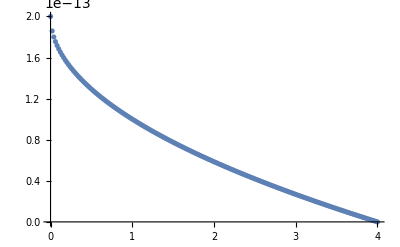

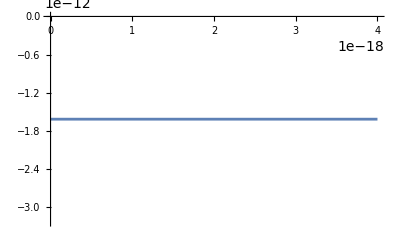

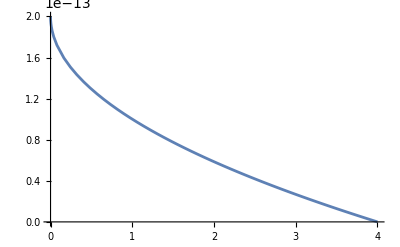

```mathematica
ListPlot[pts,PlotRange->All]
Plot[NxLeft[v2],{v2,0,v2max}]
Plot[NxLeft[v2],{v2,0,v2max},WorkingPrecision->30]
```

经过上面的排查，需要手动提升 `Plot` 的计算精度才能正确绘制，这是mma常见bug

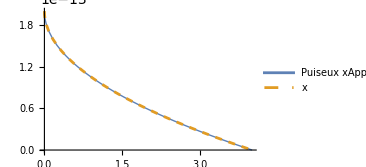
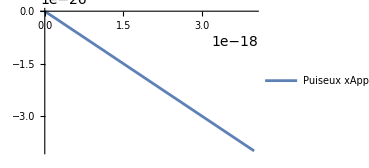

```mathematica
Plot[{xApproxLeftNumerical[v2],NxLeft[v2]},{v2,0,4.0008401621325604*10^-18},PlotStyle->{{Thick},{Dashed}},PlotLegends->{"Puiseux xApprox","x"},WorkingPrecision->30]
Plot[{xApproxLeftNumerical[v2]-NxLeft[v2]},{v2,0,4.0008401621325604*10^-18},PlotLegends->{"Puiseux xApprox-x"},WorkingPrecision->30]
```

误差的绝对值随着v2=u2-u2small增大而增大，这是正常的，因为展开中心是u2=u2small,随着x远离极小值点x0而靠近0，u=p[x]也会越来越远离u2small，任意的截断级数都会带来这样的误差。

## 用Puiseux级数形式的x(u2)求解雅可比因子 20260410

```mathematica
xApproxLeft/.testDK;
xApproxRight/.testDK(*/.abcde*);
JLeft=D[xApproxLeft, v2]/.testDK
JRight=D[xApproxRight, v2]/.testDK;
```

-(√(1/(2 CC+6 BB x0+12 AA x0^2)))/(√2 √v2)+(√v2 (6 BB+24 AA x0) (1/(2 CC+6 BB x0+12 AA x0^2))^(5/2))/(√2)-(5 v2^(3/2) (32 √2 AA (6 BB+24 AA x0) (1/(2 CC+6 BB x0+12 AA x0^2))^(9/2)+(2 (6 BB+24 AA x0)^3)/(3 (2 CC+6 BB x0+12 AA x0^2)^6)))/(2 (2 CC+6 BB x0+12 AA x0^2))-1/(2 (2 CC+6 BB x0+12 AA x0^2))7 v2^(5/2) (1/2 (6 BB+24 AA x0) (-(20 (6 BB+24 AA x0)^3)/(27 (2 CC+6 BB x0+12 AA x0^2)^8)-10 √2 (6 BB+24 AA x0) (1/(2 CC+6 BB x0+12 AA x0^2))^(9/2) (32 √2 AA (6 BB+24 AA x0) (1/(2 CC+6 BB x0+12 AA x0^2))^(9/2)+(2 (6 BB+24 AA x0)^3)/(3 (2 CC+6 BB x0+12 AA x0^2)^6)))+24 AA (-8/3 √2 (6 BB+24 AA x0)^2 (1/(2 CC+6 BB x0+12 AA x0^2))^(13/2)-(4 (32 √2 AA (6 BB+24 AA x0) (1/(2 CC+6 BB x0+12 AA x0^2))^(9/2)+(2 (6 BB+24 AA x0)^3)/(3 (2 CC+6 BB x0+12 AA x0^2)^6)))/((2 CC+6 BB x0+12 AA x0^2)^3)))

```mathematica
(*∫_0^(ϵ2-u2small) JLeft/(√(1-(v2+u2small)))ⅆv2*)
IntLeftNum=-∫_0^(ϵ2-u2small/.testparamsRN) (JLeft/(√(1-(v2+u2small)))/.x0Numerical/.abcde/.testparamsRN)ⅆv2
IntRightNum=∫_0^(1-u2small) (JRight/(√(1-(v2+u2small)))/.x0Numerical/.abcde/.testparamsRN)ⅆv2
```

2.00005000490247825303755306264566187445×10^-13+0. ⅈ

0.0001570654970669713341208934800989620892036

```mathematica
δϕApproxNum=(Re[IntRightNum]+Re[IntLeftNum] )b √(1-ϵ2)/.testparamsRN
δϕNum=NIntegrate[(b √(1-ϵ^2))/(r √(r^2-((Q^2+r (-2 M+r)) (r^2 ϵ^2-b^2 (-1+ϵ^2)))/r^2))/.testparamsRN,{r,10000,∞},WorkingPrecision->20]
```

1.570796352353276470315358875070027287832

1.5709963658233619758

```mathematica
2*1.5707963523532764-Pi
2*1.5709963658233619-Pi
Clear[b]
(4 M)/b/.testparamsRN//N
```

5.11168×10^-8

0.000400078

0.00039996

#### 20260415 排查数值residual由谁贡献，是右支积分的Puiseux近似精度不够导致，还是变量代换x->u本身的局限导致

为此，我们需要直接数值计算变量代换u(x)==u的右支解析解，并数值计算右支雅可比因子，再数值积分右支，得到解析的右支数值。将其与刚才的IntRightNum对比，即可排查是否是Puiseux的精度不够导致residual

```mathematica
(* ====================使用示例（与你原来一样）====================*)
(*步骤1：求 u=1 时的正实根 x0，用 Root 对象表示*)
Clear[x0];
p4[x0]/.testDK/.abcde/.testparamsRN;
Solve[%==0&&x0>0,x0,Reals]
xApprox/. %[[1]]/. testDK/. abcde/. testparamsRN//N
```

{{x0→2.000030000401141034141×10^-13},{x0→2.000030000401141034141×10^-13},{x0→0.5217803813047992252944366294453004585516934838},{x0→11.97821961869480076870548314234787139904554436}}

2.00003×10^-13+√v2 xk[1.]+v2 xk[2.]+v2^(3/2) xk[3.]+v2^2 xk[4.]+v2^(5/2) xk[5.]+v2^3 xk[6.]

求p (x) 极小值点，解析和数值的结果均计算

```mathematica
N[Minimize[{p[x]/.testAK/.abcde/.testparamsRN,0≤x<=1/10^4},x]]
```

{0.0000200039,{x→2.00003×10^-13}}

```mathematica
Solve[D[p[x], {x,1}]==0/.testAK/.abcde/.testparamsRN,x]//N
xsmall=Solve[D[p[x], {x,1}]==0,x,Reals][[1,1,2]]//Normal
u2small=p[xsmall]/.testAK/.abcde/.testparamsRN//N
```

{{x→2.00003×10^-13},{x→0.346111},{x→9.02889}}

Root[DD+2 CC #1+3 BB #1^2+4 AA #1^3&,1]

0.0000200039

因为 p’(x_0) = 0 ，普通 Taylor 级数无法直接反演，必须使用 Puiseux 级数（带半整数幂   \sqrt{u2 - u2small}  )。

```mathematica
Clear[getInverseSeries,xRight,xLeft];

(*1. 准备数据（必须严格这样写）*)
pnum=p[x]/. testAK/. abcde/. testparamsRN;
xsmall=NSolve[p'[x]==0/. testAK/. abcde/. testparamsRN,x,Reals][[1,1,2]];
u2small=pnum/. x->xsmall;

Print["极小值点: xsmall ≈ ",ScientificForm[xsmall,8],"   u2small ≈ ",ScientificForm[u2small,8]];

(*2. 定义局部变量和 delta（关键修正）*)
t=.;u2=.;
delta=u2-u2small;
polyDelta=(pnum/. x->xsmall+t)-u2small;

Print["二次项系数检查（应远大于 0）: ",Coefficient[polyDelta,t^2]];

Clear[getInverseSeries,xRight,xLeft];
getInverseSeries[sign_,ord_:15]:=Module[{c,s,tser,poly,eq,seriesEq,rules,k,coef,A2,c1val,sol},(*强力清理 poly*)poly=Chop[Expand[polyDelta-(polyDelta/. t->0)],10^-14];
A2=Coefficient[poly,t,2];
c1val=1/Sqrt[2 A2];
Print["二次项系数 A = ",ScientificForm[N[A2],8]];
Print["理论主导项 c1 = ",ScientificForm[N[c1val],8]];
(*初始化*)c[_]=0;
rules={c[1]->c1val};(*强制加入第一项*)tser=Sum[c[k] s^k,{k,1,ord}];
eq=Expand[poly/. t->(tser-s^2)]-delta;
seriesEq=Normal[Series[eq,{s,0,ord}]];
(*从 k=2 开始递推，严格保护 rules*)Do[coef=Chop[Coefficient[seriesEq,s^k]/. rules,10^-10];
If[coef==0,c[k]=0;
Continue[];];
sol=Quiet[Solve[coef==0,c[k]]];
If[sol==={}||Length[sol]==0,Print["停止在第 ",k," 阶（系数无法求解）"];
Break[];];
rules=Join[rules,sol[[1]]];   (*只在有解时才 Join*),{k,2,ord}];
(*输出结果*)Chop[xsmall+(tser/. rules/. s->sign Sqrt[delta]),10^-14]];

xRight[u2_]:=getInverseSeries[1];
xLeft[u2_]:=getInverseSeries[-1];
```

极小值点: xsmall ≈ 2.00003×10^-13   u2small ≈ 2.0003901×10^-5

二次项系数检查（应远大于 0）: 1.00018×10^8

```mathematica
(*诊断1：检查 polyDelta 是否正确是关于 t 的多项式*)polyDelta//Expand//Short
(*诊断2：二次项系数*)
Coefficient[polyDelta,t,2]//N
(*诊断3：当前 delta 定义*)
delta
```

5.43481×10^-22-3.51538×10^-21 t+«1»«1»2.00036×10^8 «1»+(3333266667000000 t^4)/208291667

1.00018×10^8

-0.0000200039+u2

```mathematica
(*5. 查看结果*)
xRight[u2]//Normal//Chop[#,10^-18]&
xLeft[u2]//Normal//Chop[#,10^-18]&
```

二次项系数 A = 1.00018×10^8

理论主导项 c1 = 7.0704314×10^-5

ReplaceAll::reps: {Join[{0→0.0000707043},False]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

ReplaceAll::reps: {Join[{0→0.0000707043},False,(0/.Join[{0→0.0000707043},False])==0]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

ReplaceAll::reps: {Join[{0→0.0000707043},False,(0/.Join[{0→0.0000707043},False])==0,(1.00018×10^8/.Join[{0→0.0000707043},False,(0/.Join[«2»])==0])==0]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

General::stop: 在本次计算中，ReplaceAll::reps 的进一步输出将被抑制.

二次项系数 A = 1.00018×10^8

理论主导项 c1 = 7.0704314×10^-5

ReplaceAll::reps: {Join[{0→0.0000707043},False]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

ReplaceAll::reps: {Join[{0→0.0000707043},False,(0/.Join[{0→0.0000707043},False])==0]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

ReplaceAll::reps: {Join[{0→0.0000707043},False,(0/.Join[{0→0.0000707043},False])==0,(1.00018×10^8/.Join[{0→0.0000707043},False,(0/.Join[«2»])==0])==0]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

General::stop: 在本次计算中，ReplaceAll::reps 的进一步输出将被抑制.

```mathematica
(*1. 参数准备*)
A2=Coefficient[polyDelta,t,2];          (*二次项系数*)
c1=1/Sqrt[2 A2];                          (*√项系数，正的*)
u2smallNum=u2small;                       (*极小值*)

Print["主导半解析形式："];
Print["c1 ≈ ",ScientificForm[N[c1],8]];

(*2. 左右两侧前两项近似（最可靠）*)
xRightApprox[u2_]:=xsmall+c1*Sqrt[u2-u2smallNum];
xLeftApprox[u2_]:=xsmall-c1*Sqrt[u2-u2smallNum];

(*3. 查看结果*)
xRightApprox[u2]//N//Chop[#,10^-12]&
xLeftApprox[u2]//N//Chop[#,10^-12]&
```

主导半解析形式：

c1 ≈ 7.0704314×10^-5

0.0000707043 √(-0.0000200039+u2)

-0.0000707043 √(-0.0000200039+u2)

```mathematica
(* ===推荐：更高阶 Puiseux 级数（稳定版）===*)t= .;w= .;

(*清理后的局部展开：polyLocal=A t^2+B t^3+C t^4*)
polyLocal=Chop[Expand[polyDelta-(polyDelta/. t->0)],10^-14];

Print["局部展开前4项："];
polyLocal//Normal//TraditionalForm

(*用 InverseSeries 求 t 关于 w=delta 的级数*)
wSeries=InverseSeries[Series[polyLocal,{t,0,12}],w];

(*左右两侧反函数级数（带 √w）*)
xRightSeries=xsmall+Series[Sqrt[wSeries],{w,0,8}]//Normal;
xLeftSeries=xsmall-Series[Sqrt[wSeries],{w,0,8}]//Normal;

(*定义最终函数*)
xRight[u2_]:=xRightSeries/. w->(u2-u2small);
xLeft[u2_]:=xLeftSeries/. w->(u2-u2small);

(*查看结果（建议显示到 (u2-u2small)^4 或更高）*)
xRight[u2]//Chop[#,10^-12]&
%/.u2->ϵ2/.testparamsRN//N
xLeft[u2]//Chop[#,10^-12]&
%/.u2->1//N
```

局部展开前4项：

(3333266667000000 t^4)/208291667-2.00036×10^8 t^3+1.00018×10^8 t^2

0.00999955 (-0.0000200039+u2)^(1/4)+4.99932×10^-7 (-0.0000200039+u2)^(3/4)+1.08476×10^-10 (-0.0000200039+u2)^(5/4)

4.47232×10^-7

-0.00999955 (-0.0000200039+u2)^(1/4)-4.99932×10^-7 (-0.0000200039+u2)^(3/4)-1.08476×10^-10 (-0.0000200039+u2)^(5/4)

-0.01

```mathematica
(*1. 准备四次函数px和极小值点xsmall*)
pnum=p[x]/. testAK/. abcde/. testparamsRN;   (*完全数值化后的函数*)
xsmall=NSolve[p'[x]==0/. testAK/. abcde/. testparamsRN,x,Reals][[1,1,2]]; (*取最小的临界点，即图中那个*)
u2small=pnum/. x->xsmall;

Print["极小值点: xsmall = ",xsmall,"   u2small = ",u2small];
```

极小值点: xsmall = 2.00003×10^-13   u2small = 0.0000200039

```mathematica
(*2. 局部四次展开（精确，因为原函数是四次）*)
t=.;delta=u2-u2small;
polyDelta=pnum/. x->xsmall+t-u2small;   (* =A t^2+B t^3+C t^4*)
```

```mathematica
(*3. 自动求 Puiseux 级数（半解析形式）*)
Clear[getInverseSeries];
getInverseSeries[sign_,ord_:12]:=Module[{c,s,tser,eq,eqSeries,rules,k,coef,sol},(*关键修复：使用唯一局部符号，并明确初始化*)c=Association[];(*用 Association 避免 c[0] 问题*)rules={};
tser=Sum[c[k] s^k,{k,1,ord}];
eq=polyDelta/. t->(tser-s^2);
eqSeries=Normal[Series[eq,{s,0,ord}]];
Do[coef=Coefficient[eqSeries,s^k];
(*清理 coef 中的已知规则*)coef=coef/. rules;
If[coef===0,c[k]=0;
Continue[]];
sol=Quiet@Solve[coef==0,c[k]];
If[sol==={}||Length[sol]==0,Print["无法求解到阶 ",k,"，系数为: ",coef];
Break[];];
rules=Join[rules,sol[[1]]];
c[k]=c[k]/. sol[[1]];,{k,1,ord}];
(*返回结果并清理极小虚部/噪声*)Chop[Simplify[xsmall+(tser/. rules/. s->sign Sqrt[delta])],1/10^20]]
```

```mathematica
(*4. 得到左右两侧的反函数级数*)
xRight[y_]=getInverseSeries[1,12];     (*右侧分支 x>x0*)
xLeft[y_]=getInverseSeries[-1,12];    (*左侧分支 x<x0*)
```

```mathematica
(*显示前 8 项（可自行调整阶数）*)
xRight[u2]
(Chop[#1,1/10^20]&)[Normal[xLeft[u2]]]
```

-0.0000200039+1. u2

-0.0000200039+1. u2

关于x解的渐进展开测试：

```mathematica
AsymptoticSolve[AA* x^4+BB*x^3+CC*x^2+DD*x+y==0,{x,0},{y,0,3}]
```

{{x→-y/DD-(CC y^2)/DD^3+((-2 CC^2+BB DD) y^3)/DD^5}}

```mathematica
AsymptoticSolve[AA* x^4+BB *x^3+CC *x^2+DD* x-(ϵ2+u2)==0,{x,0},{u2,0,3}]
```

{}

```mathematica
x0sols=Solve[AA* x^4+BB*x^3+CC*x^2-DD*x==0&&x>0,x,Reals]
x0=x0sols[[3,1,2]]//Normal
```

{{x→ConditionalExpression[Root[-DD+CC #1+BB #1^2+AA #1^3&,1], ]},{x→ConditionalExpression[Root[-DD+CC #1+BB #1^2+AA #1^3&,2], ]},{x→ConditionalExpression[Root[-DD+CC #1+BB #1^2+AA #1^3&,3], ]}}

Root[-DD+CC #1+BB #1^2+AA #1^3&,3]

```mathematica
x1sols=Solve[AA* x^4+BB*x^3+CC*x^2-DD*x==1&&x>0,x,Reals]
x1=x1sols[[4,1,2]]//Normal
x1n=N@x1
```

{{x→ConditionalExpression[Root[-1-DD #1+CC #1^2+BB #1^3+AA #1^4&,1], ]},{x→ConditionalExpression[Root[-1-DD #1+CC #1^2+BB #1^3+AA #1^4&,2], ]},{x→ConditionalExpression[Root[-1-DD #1+CC #1^2+BB #1^3+AA #1^4&,3], ]},{x→ConditionalExpression[Root[-1-DD #1+CC #1^2+BB #1^3+AA #1^4&,4], ]}}

Root[-1-DD #1+CC #1^2+BB #1^3+AA #1^4&,4]

Root[-1-DD #1+CC #1^2+BB #1^3+AA #1^4&,4]

```mathematica
AsymptoticSolve[AA* x^4+BB*x^3+CC*x^2-DD*x-y==0,{x,0},{y,0,6}]
AsymptoticSolve[AA x^4+BB x^3+CC x^2-DD x-(1+δ)==0,{x,x1},{δ,0,6}]
```

{{x→-y/DD+(CC y^2)/DD^3+((-2 CC^2-BB DD) y^3)/DD^5+((5 CC^3+5 BB CC DD+AA DD^2) y^4)/DD^7+((-14 CC^4-21 BB CC^2 DD-3 BB^2 DD^2-6 AA CC DD^2) y^5)/DD^9+(7 (6 CC^5+12 BB CC^3 DD+4 BB^2 CC DD^2+4 AA CC^2 DD^2+AA BB DD^3) y^6)/DD^11}}

{}

尝试失败，渐进逼近函数在常数项！=0处展不开，需要另辟蹊径。

testparams的确定需要求解近日点方程，此处从略

```mathematica
(*testparamsRN={Q->2/5,M->1,r0->10000};
SimPla={ωe[r]->√(ϵ^2 (ω∞)^2 r^-k),ωe[r0]->√(ϵ^2 (ω∞)^2 r0^-k)};
kreplace={k->0};
ToAssumptions={ℏ>0,ω∞>0,r>2 M,r0>2 M,ri>r0,rf>r0,M>0,r0>0,b>0,s[0]>0,ω∞>0,1>u>0,ϵ>0,v>0,v<1,n∞>0};
dphiodr=Simplify[-dphiodk/drodk/.spr/.{pt->ℏ ω∞,pphi->(ℏ ω∞ b)/(n∞)},Assumptions->{ℏ>0,ω∞>0}]
RNMetric={Am[r]->1-(2 M)/r+Q^2/r^2,Bm[r]->1/(1-(2 M)/r+Q^2/r^2),Cm[r]->r^2,Am[r0]->1-(2 M)/r0+Q^2/r0^2,Bm[r0]->1/(1-(2 M)/r0+Q^2/r0^2),Cm[r0]->r0^2};
Simplify[dϕodr/.RNMetric/.SimPla/.kreplace/.{n∞->1/(√(1-ϵ^2))},Assumptions->ToAssumptions];
Simplify[Denominator[%]/.{ω∞->1}];
denodphiodrsq=%^2;
Solve[%==0/.{r->r0},b];
%⟦2,1,2⟧;
Numerator[%]/r0;
-%^2;
%/.Take[testparamsRN,3];
Solve[(99999/10)^2==%,ϵ];
testparamsRN=Join[testparamsRN,%⟦2⟧];
Solve[denodphiodrsq==0/.{r->r0}/.testparamsRN,b];
testparamsRN=Join[testparamsRN,%⟦2⟧];
{ϵ2->ϵ^2/.testparamsRN};
(testparamsRN=Join[testparamsRN,%]*)testparamsRN={Q->2/5,M->1,r0->10000,ϵ->(√(199999/624875001))/4,b->999990000/(√9997800017),ϵ2->199999/9998000016};
```

#### 可积性分析 2026.04.02

接下来考察帕德逼近得到的真分式，和根式作积后得到的雅可比因子是否可积。Jacobi factor and the minimum of u2[x]

```mathematica
Clear[x0]
(*x0=x0sols⟦2,1,2⟧//Normal;*)
pade51
testAK={a[0]->ϵ^2,a[1]->DD,a[2]->CC,a[3]->BB,a[4]->AA};
abcde={AA->b^2 Q^2 (1-ϵ^2),BB->2 b^2 M (ϵ^2-1),CC->b^2 (1-ϵ^2+(Q/b)^2 ϵ^2),DD->-2 M ϵ^2,EE->ϵ^2-u2};
testparamsRN={Q->2/5,M->1,r0->10000,ϵ->(√(199999/624875001))/4,b->999990000/(√9997800017),ϵ2->199999/9998000016};
```

(x0+(u2^2 (28 a[2]^5-112 a[1] a[2]^3 a[3]+196 x0 a[2]^4 a[3]+67 a[1]^2 a[2] a[3]^2-740 x0 a[1] a[2]^2 a[3]^2+436 x0^2 a[2]^3 a[3]^2+201 x0 a[1]^2 a[3]^3-1818 x0^2 a[1] a[2] a[3]^3+96 x0^3 a[2]^2 a[3]^3-1818 x0^3 a[1] a[3]^4-765 x0^4 a[2] a[3]^4-459 x0^5 a[3]^5+100 a[1]^2 a[2]^2 a[4]-48 x0 a[1] a[2]^3 a[4]+344 x0^2 a[2]^4 a[4]-30 a[1]^3 a[3] a[4]+956 x0 a[1]^2 a[2] a[3] a[4]-1264 x0^2 a[1] a[2]^2 a[3] a[4]+1696 x0^3 a[2]^3 a[3] a[4]+2640 x0^2 a[1]^2 a[3]^2 a[4]-6280 x0^3 a[1] a[2] a[3]^2 a[4]+964 x0^4 a[2]^2 a[3]^2 a[4]-11982 x0^4 a[1] a[3]^3 a[4]-6084 x0^5 a[2] a[3]^3 a[4]-4572 x0^6 a[3]^4 a[4]-120 x0 a[1]^3 a[4]^2+1552 x0^2 a[1]^2 a[2] a[4]^2+384 x0^3 a[1] a[2]^2 a[4]^2+1888 x0^4 a[2]^3 a[4]^2+8592 x0^3 a[1]^2 a[3] a[4]^2-3392 x0^4 a[1] a[2] a[3] a[4]^2+3584 x0^5 a[2]^2 a[3] a[4]^2-30792 x0^5 a[1] a[3]^2 a[4]^2-18848 x0^6 a[2] a[3]^2 a[4]^2-18528 x0^7 a[3]^3 a[4]^2+8592 x0^4 a[1]^2 a[4]^3+4160 x0^5 a[1] a[2] a[4]^3+3776 x0^6 a[2]^2 a[4]^3-38976 x0^6 a[1] a[3] a[4]^3-29440 x0^7 a[2] a[3] a[4]^3-38832 x0^8 a[3]^2 a[4]^3-22272 x0^7 a[1] a[4]^4-20288 x0^8 a[2] a[4]^4-41280 x0^9 a[3] a[4]^4-16512 x0^10 a[4]^5))/(2 (a[1]+2 x0 a[2]+3 x0^2 a[3]+4 x0^3 a[4])^3 (7 a[2]^4-18 a[1] a[2]^2 a[3]+48 x0 a[2]^3 a[3]+3 a[1]^2 a[3]^2-96 x0 a[1] a[2] a[3]^2+120 x0^2 a[2]^2 a[3]^2-144 x0^2 a[1] a[3]^3+144 x0^3 a[2] a[3]^3+108 x0^4 a[3]^4+13 a[1]^2 a[2] a[4]-20 x0 a[1] a[2]^2 a[4]+76 x0^2 a[2]^3 a[4]+63 x0 a[1]^2 a[3] a[4]-318 x0^2 a[1] a[2] a[3] a[4]+336 x0^3 a[2]^2 a[3] a[4]-894 x0^3 a[1] a[3]^2 a[4]+489 x0^4 a[2] a[3]^2 a[4]+639 x0^5 a[3]^3 a[4]+126 x0^2 a[1]^2 a[4]^2-256 x0^3 a[1] a[2] a[4]^2+208 x0^4 a[2]^2 a[4]^2-1980 x0^4 a[1] a[3] a[4]^2+240 x0^5 a[2] a[3] a[4]^2+1398 x0^6 a[3]^2 a[4]^2-1584 x0^5 a[1] a[4]^3-368 x0^6 a[2] a[4]^3+1440 x0^7 a[3] a[4]^3+720 x0^8 a[4]^4))+(u2 (14 a[1] a[2]^4+70 x0 a[2]^5-36 a[1]^2 a[2]^2 a[3]-124 x0 a[1] a[2]^3 a[3]+568 x0^2 a[2]^4 a[3]+6 a[1]^3 a[3]^2-107 x0 a[1]^2 a[2] a[3]^2-1292 x0^2 a[1] a[2]^2 a[3]^2+1732 x0^3 a[2]^3 a[3]^2-51 x0^2 a[1]^2 a[3]^3-3546 x0^3 a[1] a[2] a[3]^3+2400 x0^4 a[2]^2 a[3]^3-3330 x0^4 a[1] a[3]^4+1611 x0^5 a[2] a[3]^4+837 x0^6 a[3]^5+26 a[1]^3 a[2] a[4]+138 x0 a[1]^2 a[2]^2 a[4]-16 x0^2 a[1] a[2]^3 a[4]+940 x0^3 a[2]^4 a[4]+96 x0 a[1]^3 a[3] a[4]+854 x0^2 a[1]^2 a[2] a[3] a[4]-3100 x0^3 a[1] a[2]^2 a[3] a[4]+5584 x0^4 a[2]^3 a[3] a[4]+1668 x0^3 a[1]^2 a[3]^2 a[4]-16402 x0^4 a[1] a[2] a[3]^2 a[4]+10330 x0^5 a[2]^2 a[3]^2 a[4]-24312 x0^5 a[1] a[3]^3 a[4]+6498 x0^6 a[2] a[3]^3 a[4]+5256 x0^7 a[3]^4 a[4]+132 x0^2 a[1]^3 a[4]^2+2056 x0^3 a[1]^2 a[2] a[4]^2-1136 x0^4 a[1] a[2]^2 a[4]^2+4656 x0^5 a[2]^3 a[4]^2+7404 x0^4 a[1]^2 a[3] a[4]^2-24224 x0^5 a[1] a[2] a[3] a[4]^2+14240 x0^6 a[2]^2 a[3] a[4]^2-69636 x0^6 a[1] a[3]^2 a[4]^2+2200 x0^7 a[2] a[3]^2 a[4]^2+11028 x0^8 a[3]^3 a[4]^2+7944 x0^5 a[1]^2 a[4]^3-11200 x0^6 a[1] a[2] a[4]^3+5728 x0^7 a[2]^2 a[4]^3-94704 x0^7 a[1] a[3] a[4]^3-20416 x0^8 a[2] a[3] a[4]^3+6408 x0^9 a[3]^2 a[4]^3-52512 x0^8 a[1] a[4]^4-23328 x0^9 a[2] a[4]^4-3840 x0^10 a[3] a[4]^4-2112 x0^11 a[4]^5))/(2 (a[1]+2 x0 a[2]+3 x0^2 a[3]+4 x0^3 a[4])^2 (7 a[2]^4-18 a[1] a[2]^2 a[3]+48 x0 a[2]^3 a[3]+3 a[1]^2 a[3]^2-96 x0 a[1] a[2] a[3]^2+120 x0^2 a[2]^2 a[3]^2-144 x0^2 a[1] a[3]^3+144 x0^3 a[2] a[3]^3+108 x0^4 a[3]^4+13 a[1]^2 a[2] a[4]-20 x0 a[1] a[2]^2 a[4]+76 x0^2 a[2]^3 a[4]+63 x0 a[1]^2 a[3] a[4]-318 x0^2 a[1] a[2] a[3] a[4]+336 x0^3 a[2]^2 a[3] a[4]-894 x0^3 a[1] a[3]^2 a[4]+489 x0^4 a[2] a[3]^2 a[4]+639 x0^5 a[3]^3 a[4]+126 x0^2 a[1]^2 a[4]^2-256 x0^3 a[1] a[2] a[4]^2+208 x0^4 a[2]^2 a[4]^2-1980 x0^4 a[1] a[3] a[4]^2+240 x0^5 a[2] a[3] a[4]^2+1398 x0^6 a[3]^2 a[4]^2-1584 x0^5 a[1] a[4]^3-368 x0^6 a[2] a[4]^3+1440 x0^7 a[3] a[4]^3+720 x0^8 a[4]^4))+(u2^3 (-14 a[2]^6+62 a[1] a[2]^4 a[3]-128 x0 a[2]^5 a[3]-25 a[1]^2 a[2]^2 a[3]^2+644 x0 a[1] a[2]^3 a[3]^2-316 x0^2 a[2]^4 a[3]^2-6 a[1]^3 a[3]^3-186 x0 a[1]^2 a[2] a[3]^3+2526 x0^2 a[1] a[2]^2 a[3]^3+420 x0^3 a[2]^3 a[3]^3-279 x0^2 a[1]^2 a[3]^4+4680 x0^3 a[1] a[2] a[3]^4+3285 x0^4 a[2]^2 a[3]^4+3510 x0^4 a[1] a[3]^5+5346 x0^5 a[2] a[3]^5+2673 x0^6 a[3]^6-74 a[1]^2 a[2]^3 a[4]-48 x0 a[1] a[2]^4 a[4]-304 x0^2 a[2]^5 a[4]+4 a[1]^3 a[2] a[3] a[4]-842 x0 a[1]^2 a[2]^2 a[3] a[4]+604 x0^2 a[1] a[2]^3 a[3] a[4]-1960 x0^3 a[2]^4 a[3] a[4]-60 x0 a[1]^3 a[3]^2 a[4]-3822 x0^2 a[1]^2 a[2] a[3]^2 a[4]+6820 x0^3 a[1] a[2]^2 a[3]^2 a[4]-1210 x0^4 a[2]^3 a[3]^2 a[4]-5310 x0^3 a[1]^2 a[3]^3 a[4]+23640 x0^4 a[1] a[2] a[3]^3 a[4]+17790 x0^5 a[2]^2 a[3]^3 a[4]+28224 x0^5 a[1] a[3]^4 a[4]+45018 x0^6 a[2] a[3]^4 a[4]+28458 x0^7 a[3]^5 a[4]+16 x0 a[1]^3 a[2] a[4]^2-1636 x0^2 a[1]^2 a[2]^2 a[4]^2-1376 x0^3 a[1] a[2]^3 a[4]^2-2648 x0^4 a[2]^4 a[4]^2-216 x0^2 a[1]^3 a[3] a[4]^2-13896 x0^3 a[1]^2 a[2] a[3] a[4]^2-3352 x0^4 a[1] a[2]^2 a[3] a[4]^2-9632 x0^5 a[2]^3 a[3] a[4]^2-26352 x0^4 a[1]^2 a[3]^2 a[4]^2+31632 x0^5 a[1] a[2] a[3]^2 a[4]^2+31676 x0^6 a[2]^2 a[3]^2 a[4]^2+91080 x0^6 a[1] a[3]^3 a[4]^2+156072 x0^7 a[2] a[3]^3 a[4]^2+129672 x0^8 a[3]^4 a[4]^2-288 x0^3 a[1]^3 a[4]^3-14328 x0^4 a[1]^2 a[2] a[4]^3-14144 x0^5 a[1] a[2]^2 a[4]^3-11136 x0^6 a[2]^3 a[4]^3-50760 x0^5 a[1]^2 a[3] a[4]^3-5808 x0^6 a[1] a[2] a[3] a[4]^3+20224 x0^7 a[2]^2 a[3] a[4]^3+153648 x0^7 a[1] a[3]^2 a[4]^3+287688 x0^8 a[2] a[3]^2 a[4]^3+326424 x0^9 a[3]^3 a[4]^3-33840 x0^6 a[1]^2 a[4]^4-22656 x0^7 a[1] a[2] a[4]^4+4448 x0^8 a[2]^2 a[4]^4+145152 x0^8 a[1] a[3] a[4]^4+290944 x0^9 a[2] a[3] a[4]^4+478992 x0^10 a[3]^2 a[4]^4+64512 x0^9 a[1] a[4]^5+129280 x0^10 a[2] a[4]^5+383616 x0^11 a[3] a[4]^5+127872 x0^12 a[4]^6))/(2 (a[1]+2 x0 a[2]+3 x0^2 a[3]+4 x0^3 a[4])^5 (7 a[2]^4-18 a[1] a[2]^2 a[3]+48 x0 a[2]^3 a[3]+3 a[1]^2 a[3]^2-96 x0 a[1] a[2] a[3]^2+120 x0^2 a[2]^2 a[3]^2-144 x0^2 a[1] a[3]^3+144 x0^3 a[2] a[3]^3+108 x0^4 a[3]^4+13 a[1]^2 a[2] a[4]-20 x0 a[1] a[2]^2 a[4]+76 x0^2 a[2]^3 a[4]+63 x0 a[1]^2 a[3] a[4]-318 x0^2 a[1] a[2] a[3] a[4]+336 x0^3 a[2]^2 a[3] a[4]-894 x0^3 a[1] a[3]^2 a[4]+489 x0^4 a[2] a[3]^2 a[4]+639 x0^5 a[3]^3 a[4]+126 x0^2 a[1]^2 a[4]^2-256 x0^3 a[1] a[2] a[4]^2+208 x0^4 a[2]^2 a[4]^2-1980 x0^4 a[1] a[3] a[4]^2+240 x0^5 a[2] a[3] a[4]^2+1398 x0^6 a[3]^2 a[4]^2-1584 x0^5 a[1] a[4]^3-368 x0^6 a[2] a[4]^3+1440 x0^7 a[3] a[4]^3+720 x0^8 a[4]^4))+(u2^4 (14 a[2]^7-46 a[1] a[2]^5 a[3]+202 x0 a[2]^6 a[3]-24 a[1]^2 a[2]^3 a[3]^2-786 x0 a[1] a[2]^4 a[3]^2+1032 x0^2 a[2]^5 a[3]^2-25 a[1]^3 a[2] a[3]^3-366 x0 a[1]^2 a[2]^2 a[3]^3-5448 x0^2 a[1] a[2]^3 a[3]^3+1528 x0^3 a[2]^4 a[3]^3-75 x0 a[1]^3 a[3]^4-1323 x0^2 a[1]^2 a[2] a[3]^4-18108 x0^3 a[1] a[2]^2 a[3]^4-4470 x0^4 a[2]^3 a[3]^4-1323 x0^3 a[1]^2 a[3]^5-28485 x0^4 a[1] a[2] a[3]^5-19440 x0^5 a[2]^2 a[3]^5-17091 x0^5 a[1] a[3]^6-25137 x0^6 a[2] a[3]^6-10773 x0^7 a[3]^7+108 a[1]^2 a[2]^4 a[4]+248 x0 a[1] a[2]^5 a[4]+652 x0^2 a[2]^6 a[4]+58 a[1]^3 a[2]^2 a[3] a[4]+1452 x0 a[1]^2 a[2]^3 a[3] a[4]+1620 x0^2 a[1] a[2]^4 a[3] a[4]+7744 x0^3 a[2]^5 a[3] a[4]+24 a[1]^4 a[3]^2 a[4]+240 x0 a[1]^3 a[2] a[3]^2 a[4]+5058 x0^2 a[1]^2 a[2]^2 a[3]^2 a[4]-8568 x0^3 a[1] a[2]^3 a[3]^2 a[4]+29340 x0^4 a[2]^4 a[3]^2 a[4]-240 x0^2 a[1]^3 a[3]^3 a[4]+2580 x0^3 a[1]^2 a[2] a[3]^3 a[4]-89130 x0^4 a[1] a[2]^2 a[3]^3 a[4]+20460 x0^5 a[2]^3 a[3]^3 a[4]-4680 x0^4 a[1]^2 a[3]^4 a[4]-224640 x0^5 a[1] a[2] a[3]^4 a[4]-108990 x0^6 a[2]^2 a[3]^4 a[4]-180684 x0^6 a[1] a[3]^5 a[4]-231228 x0^7 a[2] a[3]^5 a[4]-124416 x0^8 a[3]^6 a[4]-26 a[1]^4 a[2] a[4]^2+24 x0 a[1]^3 a[2]^2 a[4]^2+2976 x0^2 a[1]^2 a[2]^3 a[4]^2+6128 x0^3 a[1] a[2]^4 a[4]^2+10808 x0^4 a[2]^5 a[4]^2+114 x0 a[1]^4 a[3] a[4]^2+1488 x0^2 a[1]^3 a[2] a[3] a[4]^2+25392 x0^3 a[1]^2 a[2]^2 a[3] a[4]^2+26640 x0^4 a[1] a[2]^3 a[3] a[4]^2+90024 x0^5 a[2]^4 a[3] a[4]^2+528 x0^3 a[1]^3 a[3]^2 a[4]^2+46620 x0^4 a[1]^2 a[2] a[3]^2 a[4]^2-128664 x0^5 a[1] a[2]^2 a[3]^2 a[4]^2+178080 x0^6 a[2]^3 a[3]^2 a[4]^2+12996 x0^5 a[1]^2 a[3]^3 a[4]^2-719040 x0^6 a[1] a[2] a[3]^3 a[4]^2-225600 x0^7 a[2]^2 a[3]^3 a[4]^2-824400 x0^7 a[1] a[3]^4 a[4]^2-953370 x0^8 a[2] a[3]^4 a[4]^2-649566 x0^9 a[3]^5 a[4]^2+228 x0^2 a[1]^4 a[4]^3+2592 x0^3 a[1]^3 a[2] a[4]^3+29280 x0^4 a[1]^2 a[2]^2 a[4]^3+44736 x0^5 a[1] a[2]^3 a[4]^3+74928 x0^6 a[2]^4 a[4]^3+3000 x0^4 a[1]^3 a[3] a[4]^3+113328 x0^5 a[1]^2 a[2] a[3] a[4]^3-28896 x0^6 a[1] a[2]^2 a[3] a[4]^3+323712 x0^7 a[2]^3 a[3] a[4]^3+82656 x0^6 a[1]^2 a[3]^2 a[4]^3-1210176 x0^7 a[1] a[2] a[3]^2 a[4]^3-276768 x0^8 a[2]^2 a[3]^2 a[4]^3-2102616 x0^8 a[1] a[3]^3 a[4]^3-2346640 x0^9 a[2] a[3]^3 a[4]^3-2003124 x0^10 a[3]^4 a[4]^3+2400 x0^5 a[1]^3 a[4]^4+77952 x0^6 a[1]^2 a[2] a[4]^4+28032 x0^7 a[1] a[2]^2 a[4]^4+168864 x0^8 a[2]^3 a[4]^4+127872 x0^7 a[1]^2 a[3] a[4]^4-1125216 x0^8 a[1] a[2] a[3] a[4]^4-327200 x0^9 a[2]^2 a[3] a[4]^4-3178560 x0^9 a[1] a[3]^2 a[4]^4-3648000 x0^10 a[2] a[3]^2 a[4]^4-3908544 x0^11 a[3]^3 a[4]^4+63936 x0^8 a[1]^2 a[4]^5-471680 x0^9 a[1] a[2] a[4]^5-225216 x0^10 a[2]^2 a[4]^5-2684352 x0^10 a[1] a[3] a[4]^5-3264000 x0^11 a[2] a[3] a[4]^5-4724544 x0^12 a[3]^2 a[4]^5-976128 x0^11 a[1] a[4]^6-1250688 x0^12 a[2] a[4]^6-3196032 x0^13 a[3] a[4]^6-913152 x0^14 a[4]^7))/(2 (a[1]+2 x0 a[2]+3 x0^2 a[3]+4 x0^3 a[4])^7 (7 a[2]^4-18 a[1] a[2]^2 a[3]+48 x0 a[2]^3 a[3]+3 a[1]^2 a[3]^2-96 x0 a[1] a[2] a[3]^2+120 x0^2 a[2]^2 a[3]^2-144 x0^2 a[1] a[3]^3+144 x0^3 a[2] a[3]^3+108 x0^4 a[3]^4+13 a[1]^2 a[2] a[4]-20 x0 a[1] a[2]^2 a[4]+76 x0^2 a[2]^3 a[4]+63 x0 a[1]^2 a[3] a[4]-318 x0^2 a[1] a[2] a[3] a[4]+336 x0^3 a[2]^2 a[3] a[4]-894 x0^3 a[1] a[3]^2 a[4]+489 x0^4 a[2] a[3]^2 a[4]+639 x0^5 a[3]^3 a[4]+126 x0^2 a[1]^2 a[4]^2-256 x0^3 a[1] a[2] a[4]^2+208 x0^4 a[2]^2 a[4]^2-1980 x0^4 a[1] a[3] a[4]^2+240 x0^5 a[2] a[3] a[4]^2+1398 x0^6 a[3]^2 a[4]^2-1584 x0^5 a[1] a[4]^3-368 x0^6 a[2] a[4]^3+1440 x0^7 a[3] a[4]^3+720 x0^8 a[4]^4))+(u2^5 (-14 a[2]^8+68 a[1] a[2]^6 a[3]-200 x0 a[2]^7 a[3]-85 a[1]^2 a[2]^4 a[3]^2+884 x0 a[1] a[2]^5 a[3]^2-1216 x0^2 a[2]^6 a[3]^2+152 a[1]^3 a[2]^2 a[3]^3-108 x0 a[1]^2 a[2]^3 a[3]^3+6414 x0^2 a[1] a[2]^4 a[3]^3-3020 x0^3 a[2]^5 a[3]^3+36 a[1]^4 a[3]^4+1200 x0 a[1]^3 a[2] a[3]^4+3114 x0^2 a[1]^2 a[2]^2 a[3]^4+29808 x0^3 a[1] a[2]^3 a[3]^4+3579 x0^4 a[2]^4 a[3]^4+1800 x0^2 a[1]^3 a[3]^5+9828 x0^3 a[1]^2 a[2] a[3]^5+76896 x0^4 a[1] a[2]^2 a[3]^5+39348 x0^5 a[2]^3 a[3]^5+7371 x0^4 a[1]^2 a[3]^6+98172 x0^5 a[1] a[2] a[3]^6+91746 x0^6 a[2]^2 a[3]^6+49086 x0^6 a[1] a[3]^7+92664 x0^7 a[2] a[3]^7+34749 x0^8 a[3]^8+56 a[1]^2 a[2]^5 a[4]+496 x0 a[1] a[2]^6 a[4]+96 x0^2 a[2]^7 a[4]-566 a[1]^3 a[2]^3 a[3] a[4]-3236 x0 a[1]^2 a[2]^4 a[3] a[4]+1528 x0^2 a[1] a[2]^5 a[3] a[4]-1552 x0^3 a[2]^6 a[3] a[4]-a[1]^4 a[2] a[3]^2 a[4]-3278 x0 a[1]^3 a[2]^2 a[3]^2 a[4]-29898 x0^2 a[1]^2 a[2]^3 a[3]^2 a[4]-6568 x0^3 a[1] a[2]^4 a[3]^2 a[4]-19328 x0^4 a[2]^5 a[3]^2 a[4]+573 x0 a[1]^4 a[3]^3 a[4]+2058 x0^2 a[1]^3 a[2] a[3]^3 a[4]-68970 x0^3 a[1]^2 a[2]^2 a[3]^3 a[4]+30558 x0^4 a[1] a[2]^3 a[3]^3 a[4]-34308 x0^5 a[2]^4 a[3]^3 a[4]+14058 x0^3 a[1]^3 a[3]^4 a[4]-33228 x0^4 a[1]^2 a[2] a[3]^4 a[4]+336006 x0^5 a[1] a[2]^2 a[3]^4 a[4]+174546 x0^6 a[2]^3 a[3]^4 a[4]+15444 x0^5 a[1]^2 a[3]^5 a[4]+738990 x0^6 a[1] a[2] a[3]^5 a[4]+750114 x0^7 a[2]^2 a[3]^5 a[4]+513054 x0^7 a[1] a[3]^6 a[4]+1015173 x0^8 a[2] a[3]^6 a[4]+461943 x0^9 a[3]^7 a[4]+550 a[1]^4 a[2]^2 a[4]^2+2136 x0 a[1]^3 a[2]^3 a[4]^2-64 x0^2 a[1]^2 a[2]^4 a[4]^2+1952 x0^3 a[1] a[2]^5 a[4]^2-576 x0^4 a[2]^6 a[4]^2+30 a[1]^5 a[3] a[4]^2+3592 x0 a[1]^4 a[2] a[3] a[4]^2+10868 x0^2 a[1]^3 a[2]^2 a[3] a[4]^2-58248 x0^3 a[1]^2 a[2]^3 a[3] a[4]^2-64064 x0^4 a[1] a[2]^4 a[3] a[4]^2-58624 x0^5 a[2]^5 a[3] a[4]^2+8826 x0^2 a[1]^4 a[3]^2 a[4]^2+53504 x0^3 a[1]^3 a[2] a[3]^2 a[4]^2-257712 x0^4 a[1]^2 a[2]^2 a[3]^2 a[4]^2-286584 x0^5 a[1] a[2]^3 a[3]^2 a[4]^2-310704 x0^6 a[2]^4 a[3]^2 a[4]^2+96360 x0^4 a[1]^3 a[3]^3 a[4]^2-299952 x0^5 a[1]^2 a[2] a[3]^3 a[4]^2+266172 x0^6 a[1] a[2]^2 a[3]^3 a[4]^2-57624 x0^7 a[2]^3 a[3]^3 a[4]^2-98496 x0^6 a[1]^2 a[3]^4 a[4]^2+2283264 x0^7 a[1] a[2] a[3]^4 a[4]^2+2381274 x0^8 a[2]^2 a[3]^4 a[4]^2+2395386 x0^8 a[1] a[3]^5 a[4]^2+4826952 x0^9 a[2] a[3]^5 a[4]^2+2741526 x0^10 a[3]^6 a[4]^2+120 x0 a[1]^5 a[4]^3+7784 x0^2 a[1]^4 a[2] a[4]^3+35248 x0^3 a[1]^3 a[2]^2 a[4]^3-5376 x0^4 a[1]^2 a[2]^3 a[4]^3-55552 x0^5 a[1] a[2]^4 a[4]^3-57600 x0^6 a[2]^5 a[4]^3+31320 x0^3 a[1]^4 a[3] a[4]^3+222520 x0^4 a[1]^3 a[2] a[3] a[4]^3-154992 x0^5 a[1]^2 a[2]^2 a[3] a[4]^3-596544 x0^6 a[1] a[2]^3 a[3] a[4]^3-648960 x0^7 a[2]^4 a[3] a[4]^3+364776 x0^5 a[1]^3 a[3]^2 a[4]^3-390120 x0^6 a[1]^2 a[2] a[3]^2 a[4]^3-533616 x0^7 a[1] a[2]^2 a[3]^2 a[4]^3-1193280 x0^8 a[2]^3 a[3]^2 a[4]^3-392328 x0^7 a[1]^2 a[3]^3 a[4]^3+3970152 x0^8 a[1] a[2] a[3]^3 a[4]^3+3922352 x0^9 a[2]^2 a[3]^3 a[4]^3+6646464 x0^9 a[1] a[3]^4 a[4]^3+13336608 x0^10 a[2] a[3]^4 a[4]^3+9618768 x0^11 a[3]^5 a[4]^3+31320 x0^4 a[1]^4 a[4]^4+228128 x0^5 a[1]^3 a[2] a[4]^4+124800 x0^6 a[1]^2 a[2]^2 a[4]^4-269568 x0^7 a[1] a[2]^3 a[4]^4-391872 x0^8 a[2]^4 a[4]^4+600432 x0^6 a[1]^3 a[3] a[4]^4+175776 x0^7 a[1]^2 a[2] a[3] a[4]^4-748992 x0^8 a[1] a[2]^2 a[3] a[4]^4-1749632 x0^9 a[2]^3 a[3] a[4]^4-522576 x0^8 a[1]^2 a[3]^2 a[4]^4+4561952 x0^9 a[1] a[2] a[3]^2 a[4]^4+4044544 x0^10 a[2]^2 a[3]^2 a[4]^4+12002928 x0^10 a[1] a[3]^3 a[4]^4+23787168 x0^11 a[2] a[3]^3 a[4]^4+21978072 x0^12 a[3]^4 a[4]^4+343104 x0^7 a[1]^3 a[4]^5+345216 x0^8 a[1]^2 a[2] a[4]^5-179456 x0^9 a[1] a[2]^2 a[4]^5-735744 x0^10 a[2]^3 a[4]^5-349440 x0^9 a[1]^2 a[3] a[4]^5+3402112 x0^10 a[1] a[2] a[3] a[4]^5+2958080 x0^11 a[2]^2 a[3] a[4]^5+14021952 x0^11 a[1] a[3]^2 a[4]^5+27603200 x0^12 a[2] a[3]^2 a[4]^5+33419904 x0^13 a[3]^3 a[4]^5-139776 x0^10 a[1]^2 a[4]^6+1186304 x0^11 a[1] a[2] a[4]^6+1183744 x0^12 a[2]^2 a[4]^6+9644544 x0^12 a[1] a[3] a[4]^6+19016704 x0^13 a[2] a[3] a[4]^6+32720640 x0^14 a[3]^2 a[4]^6+2967552 x0^13 a[1] a[4]^7+5857280 x0^14 a[2] a[4]^7+18622464 x0^15 a[3] a[4]^7+4655616 x0^16 a[4]^8))/(2 (a[1]+2 x0 a[2]+3 x0^2 a[3]+4 x0^3 a[4])^9 (7 a[2]^4-18 a[1] a[2]^2 a[3]+48 x0 a[2]^3 a[3]+3 a[1]^2 a[3]^2-96 x0 a[1] a[2] a[3]^2+120 x0^2 a[2]^2 a[3]^2-144 x0^2 a[1] a[3]^3+144 x0^3 a[2] a[3]^3+108 x0^4 a[3]^4+13 a[1]^2 a[2] a[4]-20 x0 a[1] a[2]^2 a[4]+76 x0^2 a[2]^3 a[4]+63 x0 a[1]^2 a[3] a[4]-318 x0^2 a[1] a[2] a[3] a[4]+336 x0^3 a[2]^2 a[3] a[4]-894 x0^3 a[1] a[3]^2 a[4]+489 x0^4 a[2] a[3]^2 a[4]+639 x0^5 a[3]^3 a[4]+126 x0^2 a[1]^2 a[4]^2-256 x0^3 a[1] a[2] a[4]^2+208 x0^4 a[2]^2 a[4]^2-1980 x0^4 a[1] a[3] a[4]^2+240 x0^5 a[2] a[3] a[4]^2+1398 x0^6 a[3]^2 a[4]^2-1584 x0^5 a[1] a[4]^3-368 x0^6 a[2] a[4]^3+1440 x0^7 a[3] a[4]^3+720 x0^8 a[4]^4)))/(1+(u2 (42 a[2]^5-148 a[1] a[2]^3 a[3]+334 x0 a[2]^4 a[3]+73 a[1]^2 a[2] a[3]^2-1040 x0 a[1] a[2]^2 a[3]^2+964 x0^2 a[2]^3 a[3]^2+219 x0 a[1]^2 a[3]^3-2682 x0^2 a[1] a[2] a[3]^3+1104 x0^3 a[2]^2 a[3]^3-2682 x0^3 a[1] a[3]^4+315 x0^4 a[2] a[3]^4+189 x0^5 a[3]^5+126 a[1]^2 a[2]^2 a[4]-88 x0 a[1] a[2]^3 a[4]+580 x0^2 a[2]^4 a[4]-30 a[1]^3 a[3] a[4]+1160 x0 a[1]^2 a[2] a[3] a[4]-2236 x0^2 a[1] a[2]^2 a[3] a[4]+3400 x0^3 a[2]^3 a[3] a[4]+3054 x0^2 a[1]^2 a[3]^2 a[4]-11128 x0^3 a[1] a[2] a[3]^2 a[4]+5398 x0^4 a[2]^2 a[3]^2 a[4]-19074 x0^4 a[1] a[3]^3 a[4]-144 x0^5 a[2] a[3]^3 a[4]+558 x0^6 a[3]^4 a[4]-120 x0 a[1]^3 a[4]^2+1960 x0^2 a[1]^2 a[2] a[4]^2-368 x0^3 a[1] a[2]^2 a[4]^2+3216 x0^4 a[2]^3 a[4]^2+10104 x0^3 a[1]^2 a[3] a[4]^2-12704 x0^4 a[1] a[2] a[3] a[4]^2+9344 x0^5 a[2]^2 a[3] a[4]^2-53400 x0^5 a[1] a[3]^2 a[4]^2-8744 x0^6 a[2] a[3]^2 a[4]^2-2472 x0^7 a[3]^3 a[4]^2+10104 x0^4 a[1]^2 a[4]^3-2080 x0^5 a[1] a[2] a[4]^3+5536 x0^6 a[2]^2 a[4]^3-72240 x0^6 a[1] a[3] a[4]^3-25888 x0^7 a[2] a[3] a[4]^3-13416 x0^8 a[3]^2 a[4]^3-41280 x0^7 a[1] a[4]^4-23264 x0^8 a[2] a[4]^4-19680 x0^9 a[3] a[4]^4-7872 x0^10 a[4]^5))/(2 (a[1]+2 x0 a[2]+3 x0^2 a[3]+4 x0^3 a[4])^2 (7 a[2]^4-18 a[1] a[2]^2 a[3]+48 x0 a[2]^3 a[3]+3 a[1]^2 a[3]^2-96 x0 a[1] a[2] a[3]^2+120 x0^2 a[2]^2 a[3]^2-144 x0^2 a[1] a[3]^3+144 x0^3 a[2] a[3]^3+108 x0^4 a[3]^4+13 a[1]^2 a[2] a[4]-20 x0 a[1] a[2]^2 a[4]+76 x0^2 a[2]^3 a[4]+63 x0 a[1]^2 a[3] a[4]-318 x0^2 a[1] a[2] a[3] a[4]+336 x0^3 a[2]^2 a[3] a[4]-894 x0^3 a[1] a[3]^2 a[4]+489 x0^4 a[2] a[3]^2 a[4]+639 x0^5 a[3]^3 a[4]+126 x0^2 a[1]^2 a[4]^2-256 x0^3 a[1] a[2] a[4]^2+208 x0^4 a[2]^2 a[4]^2-1980 x0^4 a[1] a[3] a[4]^2+240 x0^5 a[2] a[3] a[4]^2+1398 x0^6 a[3]^2 a[4]^2-1584 x0^5 a[1] a[4]^3-368 x0^6 a[2] a[4]^3+1440 x0^7 a[3] a[4]^3+720 x0^8 a[4]^4)))

```mathematica
N[x0sols=Solve[p[x]==0/.testAK/.abcde/.testparamsRN,x],60]
```

{{x→-4.47216949634067984087022897645834624268971527698166567136704×10^-7 ⅈ},{x→4.47216949634067984087022897645834624268971527698166567136704×10^-7 ⅈ},{x→0.521780381305199991764941007839989388769429279040035121740947},{x→11.9782196186948000082350589921600106112305707209599648782591}}

```mathematica
xApprox/.testAK/.abcde/.testparamsRN
pade51/.testAK/.abcde/.testparamsRN
pade44/.testAK/.abcde/.testparamsRN
pade35/.testAK/.abcde/.testparamsRN
{value1,value2,value3,value4}={xApprox,pade51,pade44,pade35}/.testAK/.abcde/.testparamsRN/. u2->1//N;
{"Talor series"->value1,"[5/1] Padé"->value2,"[4/4] Padé"->value3,"[3/5] Padé"->value4}
```

0.52178-2.00344×10^-8 u2-1.50346×10^-15 u2^2-1.98805×10^-22 u2^3-2.61656×10^-29 u2^4-3.5678×10^-36 u2^5-4.85997×10^-43 u2^6

(0.52178-9.111×10^-8 u2+1.22558×10^-15 u2^2+5.99262×10^-24 u2^3+9.15024×10^-31 u2^4-3.58687×10^-39 u2^5)/(1-1.36217×10^-7 u2)

(0.52178-2.17033×10^-8 u2+2.68068×10^-13 u2^2-4.70885×10^-20 u2^3+5.78635×10^-28 u2^4)/(1-3.19835×10^-9 u2+5.16515×10^-13 u2^2-7.00418×10^-20 u2^3-4.31644×10^-29 u2^4)

(0.52178-1.57532×10^-8 u2+2.26212×10^-13 u2^2-3.68909×10^-20 u2^3)/(1+8.20492×10^-9 u2+4.36735×10^-13 u2^2-5.35283×10^-20 u2^3-7.43605×10^-28 u2^4-9.13761×10^-36 u2^5)

{Talor series→0.52178,[5/1] Padé→0.52178,[4/4] Padé→0.52178,[3/5] Padé→0.52178}

```mathematica
Root[-EE-DD #1+CC #1^2+BB #1^3+AA #1^4&,4]/.abcde/.testparamsRN/.u2->1
Root[-EE-DD #1+CC #1^2+BB #1^3+AA #1^4&,4]/.abcde/.u2->ϵ^2
N[Root[-EE-DD #1+CC #1^2+BB #1^3+AA #1^4&,4]/.abcde/.u2->ϵ^2/.testparamsRN,6]
```

Root1.00 × 10^-4Root[-249955000375-9999950 #1+24999500002500799996 #1^2+49999000005000000000 #1^3+3999920000400000000 #1^4&,4]0.00009998200380859334

Root[2 ϵ^2+2 M ϵ^2 #1+(-b^2+b^2 ϵ^2-Q^2 ϵ^2) #1^2+(-2 b^2 M+2 b^2 M ϵ^2) #1^3+(-b^2 Q^2+b^2 Q^2 ϵ^2) #1^4&,4]

6.3246×10^-7

```mathematica
Simplify[Expand[Denominator[dϕodr]/r^2]];
du2=D[1-%^2//.{r->1/x},x]dx;
J[x]=dx/du2//Simplify//Expand;
J[u2]=J[x]/.x->xtou2
Print["the Jacobian factor J[(u^2)]=dx/du^2 is saved in function J[u2]"];
```

-1/(4 xtou2^3)

the Jacobian factor J[(u^2)]=dx/du^2 is saved in function J[u2]

```mathematica
xMin=Solve[du2/dx == 0 ,x][[2,1,2]];
Simplify[Expand[Denominator[dϕodr]/r^2]];
u2Min=1-%^2//.{r->1/x}/.x->xMin;
Print["minimum of (u^2)="N[%//.{r->1/x}/.x->xMin/.testparamsRN,60]];
(*ϵ is appoximated to 0.00002000390074814339*)
```

(0.0000200039007481393866403045408056369914079858631459396480846095+0. ⅈ) minimum of (u^2)=

Do Taylor expansion on u2Min[ϵ^2] in the form of ϵ^2n

```mathematica
Series[u2Min/.ϵ^2->ϵ2,{ϵ2,0,2}]
(*CoefficientList[%,ϵ2]//.testparamsRN//N
Length[%%]*)
```

```mathematica
u2Guess=Sum[uu[i]*ϵ2^i,{i,0,2}];
u2Min/.ϵ->√ϵ2;
Solve[CoefficientList[u2Guess-%,ϵ2]==0,{uu[0],uu[1],uu[2]}]
```

$Aborted

Do Taylor expansion on J[u2] in the form of (u2-u2Min)^n

```mathematica
J[u2];
%/.u2->{u0+u2mu2smallRN} 
(*here we use u0 to replace uMin temporarily*)
Coefficient[%,u2mu2smallRN]
```

{-(1/(2 (ϵ^2 (M-Q^2 (M/(2 Q^2)-1/2 √(M^2/Q^4-(-b^2+b^2 ϵ^2-Q^2 ϵ^2)/(b^2 Q^2 (-1+ϵ^2))+(b^2-b^2 ϵ^2+Q^2 ϵ^2)/(3 (b^2 Q^2-b^2 Q^2 ϵ^2))+(2^(1/3) (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)))/(3 (b^2 Q^2-b^2 Q^2 ϵ^2) (108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3))+1/(3 2^(1/3) (b^2 Q^2-b^2 Q^2 ϵ^2))(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3))-1/2 √((2 M^2)/Q^4-(-b^2+b^2 ϵ^2-Q^2 ϵ^2)/(b^2 Q^2 (-1+ϵ^2))-(b^2-b^2 ϵ^2+Q^2 ϵ^2)/(3 (b^2 Q^2-b^2 Q^2 ϵ^2))-(2^(1/3) (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)))/(3 (b^2 Q^2-b^2 Q^2 ϵ^2) (108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3))-1/(3 2^(1/3) (b^2 Q^2-b^2 Q^2 ϵ^2))(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3)-((8 M^3)/Q^6-(16 M ϵ^2)/(b^2 Q^2 (-1+ϵ^2))-(8 M (-b^2+b^2 ϵ^2-Q^2 ϵ^2))/(b^2 Q^4 (-1+ϵ^2)))/(4 √(M^2/Q^4-(-b^2+b^2 ϵ^2-Q^2 ϵ^2)/(b^2 Q^2 (-1+ϵ^2))+(b^2-b^2 ϵ^2+Q^2 ϵ^2)/(3 (b^2 Q^2-b^2 Q^2 ϵ^2))+(2^(1/3) (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)))/(3 (b^2 Q^2-b^2 Q^2 ϵ^2) (108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3))+1/(3 2^(1/3) (b^2 Q^2-b^2 Q^2 ϵ^2))(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3))))))+b^2 (-1+ϵ^2) (M/(2 Q^2)-1/2 √(M^2/Q^4-(-b^2+b^2 ϵ^2-Q^2 ϵ^2)/(b^2 Q^2 (-1+ϵ^2))+(b^2-b^2 ϵ^2+Q^2 ϵ^2)/(3 (b^2 Q^2-b^2 Q^2 ϵ^2))+(2^(1/3) (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)))/(3 (b^2 Q^2-b^2 Q^2 ϵ^2) (108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3))+1/(3 2^(1/3) (b^2 Q^2-b^2 Q^2 ϵ^2))(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3))-1/2 √((2 M^2)/Q^4-(-b^2+b^2 ϵ^2-Q^2 ϵ^2)/(b^2 Q^2 (-1+ϵ^2))-(b^2-b^2 ϵ^2+Q^2 ϵ^2)/(3 (b^2 Q^2-b^2 Q^2 ϵ^2))-(2^(1/3) (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)))/(3 (b^2 Q^2-b^2 Q^2 ϵ^2) (108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3))-1/(3 2^(1/3) (b^2 Q^2-b^2 Q^2 ϵ^2))(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3)-((8 M^3)/Q^6-(16 M ϵ^2)/(b^2 Q^2 (-1+ϵ^2))-(8 M (-b^2+b^2 ϵ^2-Q^2 ϵ^2))/(b^2 Q^4 (-1+ϵ^2)))/(4 √(M^2/Q^4-(-b^2+b^2 ϵ^2-Q^2 ϵ^2)/(b^2 Q^2 (-1+ϵ^2))+(b^2-b^2 ϵ^2+Q^2 ϵ^2)/(3 (b^2 Q^2-b^2 Q^2 ϵ^2))+(2^(1/3) (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)))/(3 (b^2 Q^2-b^2 Q^2 ϵ^2) (108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3))+1/(3 2^(1/3) (b^2 Q^2-b^2 Q^2 ϵ^2))(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3))))) (1-3 M (M/(2 Q^2)-1/2 √(M^2/Q^4-(-b^2+b^2 ϵ^2-Q^2 ϵ^2)/(b^2 Q^2 (-1+ϵ^2))+(b^2-b^2 ϵ^2+Q^2 ϵ^2)/(3 (b^2 Q^2-b^2 Q^2 ϵ^2))+(2^(1/3) (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)))/(3 (b^2 Q^2-b^2 Q^2 ϵ^2) (108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3))+1/(3 2^(1/3) (b^2 Q^2-b^2 Q^2 ϵ^2))(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3))-1/2 √((2 M^2)/Q^4-(-b^2+b^2 ϵ^2-Q^2 ϵ^2)/(b^2 Q^2 (-1+ϵ^2))-(b^2-b^2 ϵ^2+Q^2 ϵ^2)/(3 (b^2 Q^2-b^2 Q^2 ϵ^2))-(2^(1/3) (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)))/(3 (b^2 Q^2-b^2 Q^2 ϵ^2) (108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3))-1/(3 2^(1/3) (b^2 Q^2-b^2 Q^2 ϵ^2))(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3)-((8 M^3)/Q^6-(16 M ϵ^2)/(b^2 Q^2 (-1+ϵ^2))-(8 M (-b^2+b^2 ϵ^2-Q^2 ϵ^2))/(b^2 Q^4 (-1+ϵ^2)))/(4 √(M^2/Q^4-(-b^2+b^2 ϵ^2-Q^2 ϵ^2)/(b^2 Q^2 (-1+ϵ^2))+(b^2-b^2 ϵ^2+Q^2 ϵ^2)/(3 (b^2 Q^2-b^2 Q^2 ϵ^2))+(2^(1/3) (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)))/(3 (b^2 Q^2-b^2 Q^2 ϵ^2) (108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3))+1/(3 2^(1/3) (b^2 Q^2-b^2 Q^2 ϵ^2))(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3)))))+2 Q^2 ((M/(2 Q^2)-1/2 √(M^2/Q^4-(-b^2+b^2 ϵ^2-Q^2 ϵ^2)/(b^2 Q^2 (-1+ϵ^2))+(b^2-b^2 ϵ^2+Q^2 ϵ^2)/(3 (b^2 Q^2-b^2 Q^2 ϵ^2))+(2^(1/3) (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)))/(3 (b^2 Q^2-b^2 Q^2 ϵ^2) (108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3))+1/(3 2^(1/3) (b^2 Q^2-b^2 Q^2 ϵ^2))(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3))-1/2 √((2 M^2)/Q^4-(-b^2+b^2 ϵ^2-Q^2 ϵ^2)/(b^2 Q^2 (-1+ϵ^2))-(b^2-b^2 ϵ^2+Q^2 ϵ^2)/(3 (b^2 Q^2-b^2 Q^2 ϵ^2))-(2^(1/3) (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)))/(3 (b^2 Q^2-b^2 Q^2 ϵ^2) (108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3))-1/(3 2^(1/3) (b^2 Q^2-b^2 Q^2 ϵ^2))(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3)-((8 M^3)/Q^6-(16 M ϵ^2)/(b^2 Q^2 (-1+ϵ^2))-(8 M (-b^2+b^2 ϵ^2-Q^2 ϵ^2))/(b^2 Q^4 (-1+ϵ^2)))/(4 √(M^2/Q^4-(-b^2+b^2 ϵ^2-Q^2 ϵ^2)/(b^2 Q^2 (-1+ϵ^2))+(b^2-b^2 ϵ^2+Q^2 ϵ^2)/(3 (b^2 Q^2-b^2 Q^2 ϵ^2))+(2^(1/3) (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)))/(3 (b^2 Q^2-b^2 Q^2 ϵ^2) (108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3))+1/(3 2^(1/3) (b^2 Q^2-b^2 Q^2 ϵ^2))(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2)+√(-4 (12 M ϵ^2 (-b^2 M+b^2 M ϵ^2)+(b^2-b^2 ϵ^2+Q^2 ϵ^2)^2+12 (-u0-u2mu2smallRN+ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^3+(108 (-u0-u2mu2smallRN+ϵ^2) (-b^2 M+b^2 M ϵ^2)^2+36 M ϵ^2 (-b^2 M+b^2 M ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2)+2 (b^2-b^2 ϵ^2+Q^2 ϵ^2)^3+108 M^2 ϵ^4 (b^2 Q^2-b^2 Q^2 ϵ^2)-72 (-u0-u2mu2smallRN+ϵ^2) (b^2-b^2 ϵ^2+Q^2 ϵ^2) (b^2 Q^2-b^2 Q^2 ϵ^2))^2))^(1/3))))))^2))))}

{0}

```mathematica
J1Mu1=Series[%,{u2mu2smallRN,0,1}];
Coefficient[J1Mu1,u2mu2smallRN]
```

0